## 1D chain

### Test

```mathematica
dim = 10; ω=0.1*10^12;
MGe=1.2*10^-25;MSi=4.7*10^-26;KGe=13.7;KSi=16.9;
Mab = (MGe+MSi)/2;Kab =Kbc= (KGe+KSi)/2;
 M =MGe; Kdiag=KGe; Koff=KGe;  ωcab=ωcbc=2√(Kab/Mab);

mass = SparseArray[{{i_,i_}->M},{dim,dim}];
springC = SparseArray[{{i_,i_}->2 Kdiag,{i_,j_}/;Abs[i-j]==1->-Koff},{dim,dim}];

(*Self energies*)
Σab = - Kab Exp[2 ⅈ ArcSin[ω/ωcab]];Σbc = - Kbc Exp[2 ⅈ ArcSin[ω/ωcbc]];
Σabmat = SparseArray[{{i_,j_}/;i==j==1->Σab},{dim,dim}];
Σbcmat = SparseArray[{{i_,j_}/;i==j==dim->Σbc},{dim,dim}];

(*Broadening factors*)
(*Γab = 4 Kab (ω/ωcab)√(1-(ω/ωcab)^2); Γbc = 4 Kbc (ω/ωcbc)√(1-(ω/ωcbc)^2);
Γabmat = SparseArray[{{i_,j_}/;i==j==1->Γab},{dim,dim}];
Γbcmat = SparseArray[{{i_,j_}/;i==j==1->Γbc},{dim,dim}];*)
Γab = -2  Im[Σabmat] ; Γbc = - 2 Im[Σbcmat];

Map[MatrixForm,{mass,springC,Σabmat,Σbcmat,Γab,Γbc}]

(*Green's function*)
GR = Inverse[(mass ω^2 - springC -  Σabmat -  Σbcmat )];
GA=ConjugateTranspose[GR];

(*Transmission*)
transmission =  Tr[Γab.GR.Γbc.GA]
```

{(1.2×10^-25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.2×10^-25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.2×10^-25 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.2×10^-25 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1.2×10^-25 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1.2×10^-25 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1.2×10^-25 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.2×10^-25 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.2×10^-25 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.2×10^-25),(27.4 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-13.7 | 27.4 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -13.7 | 27.4 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -13.7 | 27.4 | -13.7 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -13.7 | 27.4 | -13.7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -13.7 | 27.4 | -13.7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -13.7 | 27.4 | -13.7 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 27.4 | -13.7 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 27.4 | -13.7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 27.4),(-15.2996-0.113028 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(-15.2996-0.113028 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0.226056 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0.226056 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

0.000211731+0. ⅈ

### 1D chain

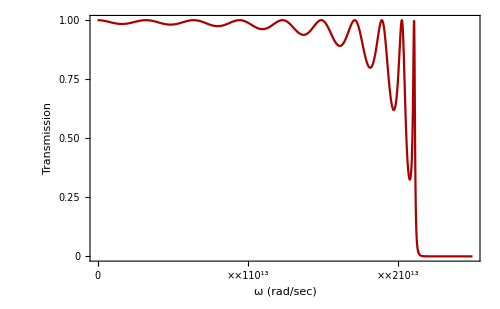

```mathematica
dim = 10;
MGe=1.2*10^-25;MSi=4.7*10^-26;KGe=13.7;KSi=16.9;
Mab =Mbc= (MGe+MSi)/2;Kab =Kbc= (KGe+KSi)/2;
 M =MGe; Kdiag=KGe; Koff=KGe;  ωcab=ωcbc=2√(Kab/Mab);

mass = SparseArray[{{i_,i_}->M},{dim,dim}];
springC = SparseArray[{{i_,j_}/;i==j && i!=1&&i!=dim->2 Kdiag,{i_,j_}/;i==j==1->KGe+Kab,{i_,j_}/;i==j==dim->KGe+Kbc,{i_,j_}/;Abs[i-j]==1->-Koff},{dim,dim}];

leftω=0.0001*10^12; rightω=2.5*10^13; stepω =0.01*10^12;
transmission=ParallelTable[
Σab = - Kab Exp[2 ⅈ ArcSin[ω/ωcab]];Σbc = - Kbc Exp[2 ⅈ ArcSin[ω/ωcbc]];
Σabmat = SparseArray[{{i_,j_}/;i==j==1->Σab},{dim,dim}];
Σbcmat = SparseArray[{{i_,j_}/;i==j==dim->Σbc},{dim,dim}];
Γab = -2  Im[Σabmat] ; Γbc = - 2 Im[Σbcmat];
(*Green's function*)
GR = Inverse[(mass ω^2 - springC -  Σabmat -  Σbcmat )];
GA=ConjugateTranspose[GR];
{ω, Chop[ Tr[Γab.GR.Γbc.GA]]},{ω,leftω,rightω,stepω}];
tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

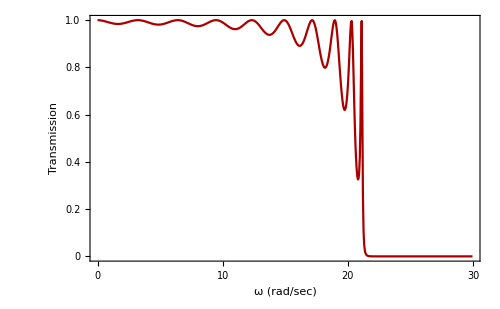

```mathematica
(*Converting mass into THz unit*)
dim = 10;
MGe=.12;MSi=.047;KGe=13.7;KSi=16.9;
Mab =Mbc=(MGe+MSi)/2;Kab =Kbc=(KGe+KSi)/2;
 M =MGe; Kdiag=KGe; Koff=KGe;  ωcab=ωcbc=2√(Kab/Mab);

mass = SparseArray[{{i_,i_}->M},{dim,dim}];
springC = SparseArray[{{i_,j_}/;i==j && i!=1&&i!=dim->2 Kdiag,{i_,j_}/;i==j==1->KGe+Kab,{i_,j_}/;i==j==dim->KGe+Kbc,{i_,j_}/;Abs[i-j]==1->-Koff},{dim,dim}];

leftω=0.0001; rightω=30; stepω =0.05;
transmission=ParallelTable[
Σab = - Kab Exp[2 ⅈ ArcSin[ω/ωcab]];Σbc = - Kbc Exp[2 ⅈ ArcSin[ω/ωcbc]];
Σabmat = SparseArray[{{i_,j_}/;i==j==1->Σab},{dim,dim}];
Σbcmat = SparseArray[{{i_,j_}/;i==j==dim->Σbc},{dim,dim}];
Γab = ⅈ(Σabmat-ConjugateTranspose[Σabmat]) ; Γbc = ⅈ(Σbcmat-ConjugateTranspose[Σbcmat]);
(*Green's function*)
GR = Inverse[(mass ω^2 - springC -  Σabmat -  Σbcmat )];
GA=ConjugateTranspose[GR];
{ω, Chop[ Tr[Γab.GR.Γbc.GA]]},{ω,leftω,rightω,stepω}];
tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

### By solving Dyson equation (single ω)

```mathematica
(******************************************Parameters********************************)
channelLength = 10; channelWidth=1;
mChannel =.12; mSource=.047; mDrain=.047;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;
kChannel = 13.7; kSource=16.9; kDrain=16.9;
kSC = (kChannel+kSource)/2; kCD = (kChannel+kDrain)/2;
η=0.00001;

(**********************************Surface for Channel******************************************)
αSurfaceL= DiagonalMatrix[Table[kChannel+kSC,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αSurfaceR= DiagonalMatrix[Table[kChannel+kCD,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αSurfaceR//MatrixForm;

(**********************************Channel******************************************)
αChannel= DiagonalMatrix[Table[2kChannel,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αChannel//MatrixForm;

βChannel=DiagonalMatrix[Table[kChannel,channelWidth]];
βChannel//MatrixForm;

MChannel = SparseArray[{{i_,i_}->mChannel},{channelWidth*channelLength ,channelWidth*channelLength }];
KChannel = SparseArray[{Band[{1,1}]->Table[If[i==1,αSurfaceL,If[i==channelLength,αSurfaceR,αChannel]],{i,1,channelLength }],Band[{1,channelWidth+1}]->Table[-βChannel,{channelLength -1}],Band[{channelWidth+1,1}]->Table[-βChannel,{channelLength -1}]},{channelWidth*channelLength ,channelWidth*channelLength } ];
KChannel//MatrixForm;

(**********************************Couplings******************************************)
cSource = DiagonalMatrix[Table[-kSC,channelWidth]];
cDrain = DiagonalMatrix[Table[-kCD,channelWidth]];

(**********************************Leads******************************************)
αSource=DiagonalMatrix[Table[kSource+kSC,channelWidth]];
αDrain=DiagonalMatrix[Table[kDrain+kCD,channelWidth]];

βSource=DiagonalMatrix[Table[-kSource,channelWidth]];
βDrain=DiagonalMatrix[Table[-kDrain,channelWidth]];

ω1=0.001;
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSC ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.(βSource^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(channelWidth-1)},{j,1,Length@KChannel-(channelWidth-1)}]]
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mCD ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.(βDrain^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}]];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(channelWidth-1),ConjugateTranspose[cDrain].Partition[Values[sol],{Length@cDrain}].cDrain,0],{i,1,Length@KChannel-(channelWidth-1)},{j,1,Length@KChannel-(channelWidth-1)}]]
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[(MChannel IdentityMatrix[Length@KChannel] ω1^2 - KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
Chop[ Tr[ΓS.GR.ΓD.GA]]
```

{{-13.1958-4.21125 ⅈ,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-13.1958-4.21125 ⅈ}}

0.167638

### By solving Dyson equation (ω variation)

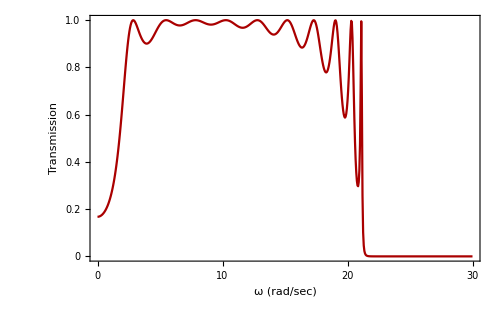

```mathematica
(******************************************Parameters********************************)
channelLength = 10; channelWidth=1;
mChannel =.12; mSource=.047; mDrain=.047;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;
kChannel = 13.7; kSource=16.9; kDrain=16.9;
kSC = (kChannel+kSource)/2; kCD = (kChannel+kDrain)/2;
η=0.00001;

(**********************************Surface for Channel******************************************)
αSurfaceL= DiagonalMatrix[Table[kChannel+kSC,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αSurfaceR= DiagonalMatrix[Table[kChannel+kCD,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αSurfaceR//MatrixForm;

(**********************************Channel******************************************)
αChannel= DiagonalMatrix[Table[2kChannel,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αChannel//MatrixForm;

βChannel=DiagonalMatrix[Table[kChannel,channelWidth]];
βChannel//MatrixForm;

MChannel = SparseArray[{{i_,i_}->mChannel},{channelWidth*channelLength ,channelWidth*channelLength }];
KChannel = SparseArray[{Band[{1,1}]->Table[If[i==1,αSurfaceL,If[i==channelLength,αSurfaceR,αChannel]],{i,1,channelLength }],Band[{1,channelWidth+1}]->Table[-βChannel,{channelLength -1}],Band[{channelWidth+1,1}]->Table[-βChannel,{channelLength -1}]},{channelWidth*channelLength ,channelWidth*channelLength } ];
KChannel//MatrixForm;

(**********************************Couplings******************************************)
cSource = DiagonalMatrix[Table[kSC ,channelWidth]];
cDrain = DiagonalMatrix[Table[kCD ,channelWidth]];

(**********************************Leads******************************************)
αSource=DiagonalMatrix[Table[kSource+kSC,channelWidth]];
αDrain=DiagonalMatrix[Table[kDrain+kCD,channelWidth]];

βSource=DiagonalMatrix[Table[kSource,channelWidth]];
βDrain=DiagonalMatrix[Table[kDrain,channelWidth]];

transmission=Table[
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSC ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.(βSource^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(channelWidth-1)},{j,1,Length@KChannel-(channelWidth-1)}]];
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mCD ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.(βDrain^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}]];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(channelWidth-1),ConjugateTranspose[cDrain].Partition[Values[sol],{Length@cDrain}].cDrain,0],{i,1,Length@KChannel-(channelWidth-1)},{j,1,Length@KChannel-(channelWidth-1)}]];
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[(MChannel IdentityMatrix[Length@KChannel] ω1^2 - KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,-.001,30,.05}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

### Final code (Comparing two codes)

The value of Mab and Kab : 0.0835 15.3

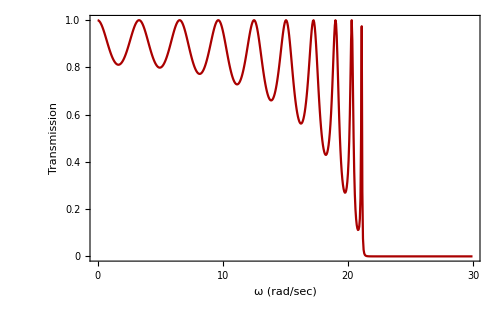

```mathematica
(*Converting mass into THz unit*)
dim = 10;
MGe=.12;MSi=.047;KGe=13.7;KSi=16.9;
Mab =Mbc=(MGe+MSi)/2;Kab =Kbc=(KGe+KSi)/2;
 M =MGe; Kdiag=KGe; Koff=KGe;  ωcab=ωcbc=2√(KSi/MSi);
Print["The value of Mab and Kab : " ,Mab," ", Kab]

mass = SparseArray[{{i_,i_}->M},{dim,dim}];
springC = SparseArray[{{i_,j_}/;i==j && i!=1&&i!=dim->2 Kdiag,{i_,j_}/;i==j==1->KGe+Kab,{i_,j_}/;i==j==dim->KGe+Kbc,{i_,j_}/;Abs[i-j]==1->-Koff},{dim,dim}];

leftω=0.01; rightω=30; stepω =0.05;
transmission=ParallelTable[
Σab = - Kab Exp[2 ⅈ ArcSin[ω/ωcab]];Σbc = - Kbc Exp[2 ⅈ ArcSin[ω/ωcbc]];
Σabmat = SparseArray[{{i_,j_}/;i==j==1->Σab},{dim,dim}];
Σbcmat = SparseArray[{{i_,j_}/;i==j==dim->Σbc},{dim,dim}];
Γab = ⅈ(Σabmat-ConjugateTranspose[Σabmat]) ; Γbc = ⅈ(Σbcmat-ConjugateTranspose[Σbcmat]);
(*Green's function*)
GR = Inverse[(mass ω^2 - springC -  Σabmat -  Σbcmat )];
GA=ConjugateTranspose[GR];
{ω, Chop[ Tr[Γab.GR.Γbc.GA]]},{ω,leftω,rightω,stepω}];
tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
plotOld=ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

(29. | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-13.7 | 27.4 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -13.7 | 27.4 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -13.7 | 27.4 | -13.7 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -13.7 | 27.4 | -13.7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -13.7 | 27.4 | -13.7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -13.7 | 27.4 | -13.7 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 27.4 | -13.7 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 27.4 | -13.7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 29.)

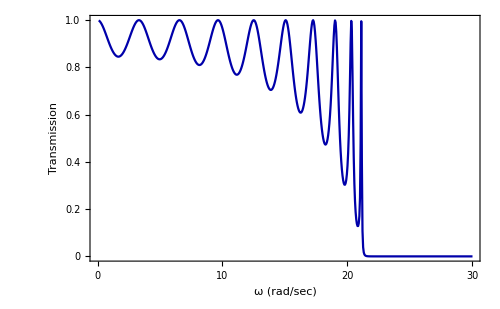

```mathematica
(******************************************Parameters********************************)
channelLength = 10; channelWidth=1;
mChannel =.12; mSource=0.047(*.047*); mDrain=mSource(*.047*);
kChannel = 13.7; kSource=15.3(*16.9*); kDrain=kSource(*16.9*);
mSC=0.0835(*(mChannel+mSource)/2*); mCD = mSC(*(mChannel+mDrain)/2*);
kSC = 15.3(*15.3(kChannel+kSource)/2*); kCD = kSC(*(kChannel+kDrain)/2*);
η=0.00001;

(**********************************Surface for Channel******************************************)
αSurfaceL= DiagonalMatrix[Table[ kChannel+kSC,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αSurfaceR= DiagonalMatrix[Table[ kChannel+kCD,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αSurfaceR//MatrixForm;

(**********************************Channel******************************************)
αChannel= DiagonalMatrix[Table[2kChannel,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αChannel//MatrixForm;

βChannel=DiagonalMatrix[Table[kChannel,channelWidth]];
βChannel//MatrixForm;

MChannel = SparseArray[{{i_,i_}->mChannel},{channelWidth*channelLength ,channelWidth*channelLength }];
KChannel = SparseArray[{Band[{1,1}]->Table[If[i==1,αSurfaceL,If[i==channelLength,αSurfaceR,αChannel]],{i,1,channelLength }],Band[{1,channelWidth+1}]->Table[-βChannel,{channelLength -1}],Band[{channelWidth+1,1}]->Table[-βChannel,{channelLength -1}]},{channelWidth*channelLength ,channelWidth*channelLength } ];
KChannel//MatrixForm

(**********************************Couplings******************************************)
cSource = DiagonalMatrix[Table[kSC ,channelWidth]];
cDrain = DiagonalMatrix[Table[kCD ,channelWidth]];

(**********************************Leads******************************************)
αSource=DiagonalMatrix[Table[kSource+kSC,channelWidth]];
αDrain=DiagonalMatrix[Table[kDrain+kCD,channelWidth]];

βSource=DiagonalMatrix[Table[kSource,channelWidth]];
βDrain=DiagonalMatrix[Table[kDrain,channelWidth]];

transmission=Table[
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSource ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.(βSource^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(channelWidth-1)},{j,1,Length@KChannel-(channelWidth-1)}]];
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mDrain ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.(βDrain^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}]];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(channelWidth-1),ConjugateTranspose[cDrain].Partition[Values[sol],{Length@cDrain}].cDrain,0],{i,1,Length@KChannel-(channelWidth-1)},{j,1,Length@KChannel-(channelWidth-1)}]];
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[(MChannel IdentityMatrix[Length@KChannel] ω1^2 - KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.1,30,.05}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
plotD=ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Blue],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

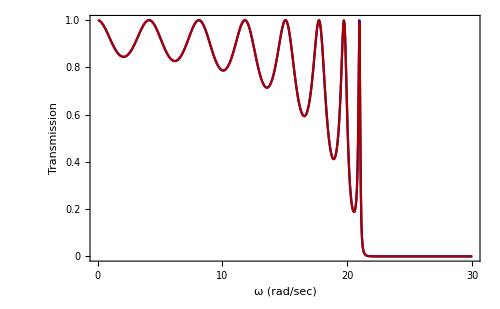

```mathematica
Show[plotD,plotOld]
```

(1.8 | -1. | 0 | 0 | 0 | 0 | 0 | 0
-1. | 2. | -1. | 0 | 0 | 0 | 0 | 0
0 | -1. | 2. | -1. | 0 | 0 | 0 | 0
0 | 0 | -1. | 2. | -1. | 0 | 0 | 0
0 | 0 | 0 | -1. | 2. | -1. | 0 | 0
0 | 0 | 0 | 0 | -1. | 2. | -1. | 0
0 | 0 | 0 | 0 | 0 | -1. | 2. | -1.
0 | 0 | 0 | 0 | 0 | 0 | -1. | 1.8)

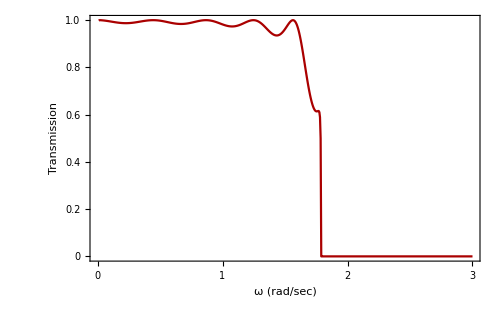

```mathematica
(******************************************Parameters********************************)
channelLength = 8; channelWidth=1;
mChannel =1(*.12*); mSource=1.(*.047*); mDrain=mSource(*.047*);
kChannel = 1.(*13.7*); kSource=.8(*16.9*); kDrain=kSource(*16.9*);
mSC=1(*(mChannel+mSource)/2*); mCD = mSC(*(mChannel+mDrain)/2*);
kSC = .8(*(kChannel+kSource)/2*); kCD = kSC(*(kChannel+kDrain)/2*);
η=0.00001;

(**********************************Surface for Channel******************************************)
αSurfaceL= DiagonalMatrix[Table[ kChannel+kSC,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αSurfaceR= DiagonalMatrix[Table[ kChannel+kCD,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αSurfaceR//MatrixForm;

(**********************************Channel******************************************)
αChannel= DiagonalMatrix[Table[2kChannel,channelWidth]](*+If[channelWidth>1,DiagonalMatrix[Table[tV,channelWidth-1],1]+DiagonalMatrix[Table[tV,channelWidth-1],-1],0]*);
αChannel//MatrixForm;

βChannel=DiagonalMatrix[Table[kChannel,channelWidth]];
βChannel//MatrixForm;

MChannel = SparseArray[{{i_,i_}->mChannel},{channelWidth*channelLength ,channelWidth*channelLength }];
KChannel = SparseArray[{Band[{1,1}]->Table[If[i==1,αSurfaceL,If[i==channelLength,αSurfaceR,αChannel]],{i,1,channelLength }],Band[{1,channelWidth+1}]->Table[-βChannel,{channelLength -1}],Band[{channelWidth+1,1}]->Table[-βChannel,{channelLength -1}]},{channelWidth*channelLength ,channelWidth*channelLength } ];
KChannel//MatrixForm

(**********************************Couplings******************************************)
cSource = DiagonalMatrix[Table[kSC ,channelWidth]];
cDrain = DiagonalMatrix[Table[kCD ,channelWidth]];

(**********************************Leads******************************************)
αSource=DiagonalMatrix[Table[kSource+kSC,channelWidth]];
αDrain=DiagonalMatrix[Table[kDrain+kCD,channelWidth]];

βSource=DiagonalMatrix[Table[kSource,channelWidth]];
βDrain=DiagonalMatrix[Table[kDrain,channelWidth]];

transmission=Table[
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSource ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.(βSource^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(channelWidth-1)},{j,1,Length@KChannel-(channelWidth-1)}]];
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mDrain ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.(βDrain^2).GS11-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}]];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(channelWidth-1),ConjugateTranspose[cDrain].Partition[Values[sol],{Length@cDrain}].cDrain,0],{i,1,Length@KChannel-(channelWidth-1)},{j,1,Length@KChannel-(channelWidth-1)}]];
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[(MChannel IdentityMatrix[Length@KChannel] ω1^2 - KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.01,3,.005}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

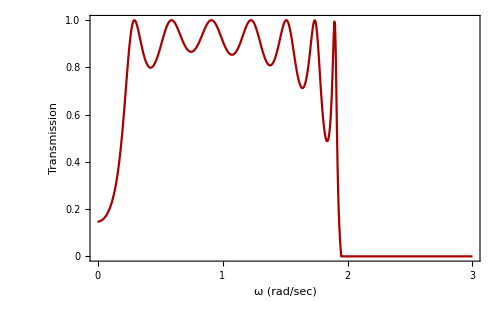

## 1D chain to Square Lattice

### Model

```mathematica
(********************************************* Function to generate spring between two points *********************************************)
generateSpring[p1_,p2_,turns_,springRadius_,tubeRadius_]:=Module[{vector,length,direction,helixPath,alignmentMatrix},
vector=p2-p1;
length=Norm[vector];
(*Handle the degenerate case where the points coincide*)
If[length==0,Return[Graphics3D[]]];
direction=vector/length;(*Normalize the direction vector*)
helixPath=Table[{springRadius Cos[2 Pi turns z/length],springRadius Sin[2 Pi turns z/length],z},{z,0,length,0.01}];(* helical path along the z-axis*)
alignmentMatrix=RotationMatrix3D[VectorAngle[{0,0,1},direction],Cross[{0,0,1},direction]];
helixPath=Map[alignmentMatrix.#+p1&,helixPath];(*Apply the alignment and translate the helix to p1*)
Graphics3D[{Black,Tube[helixPath,tubeRadius]}]];

(*Rotation matrix in 3D for a given axis and angle*)
RotationMatrix3D[angle_,axis_]:=Module[{c=Cos[angle],s=Sin[angle],v=1-Cos[angle],x,y,z},{x,y,z}=Normalize[axis];
{{x x v+c,x y v-z s,x z v+y s},{x y v+z s,y y v+c,y z v-x s},{x z v-y s,y z v+x s,z z v+c}}];

(********************************************* Function to generate Lattice coordinates******************************************************)
squareLatticeCoordinates[length_,width_,ax_,ay_]:=Module[{coordinates},coordinates=Table[{i*ax,j*ay},{i,0,length-1},{j,0,width-1}];Flatten[coordinates,1]];

(********************************************* Function to generate hoppings along x and y directions *********************************************)
generateHoppings[coordinates_,ax_,ay_]:=Module[{hoppings,neighbors,xHop,yHop,tx=1,ty=1},xHop={tx,{ax,0}};yHop={ty,{0,ay}};hoppings=Flatten[Table[neighbors={};
If[MemberQ[coordinates,coord+xHop[[2]]],AppendTo[neighbors,{coord,coord+xHop[[2]]}]];
If[MemberQ[coordinates,coord+yHop[[2]]],AppendTo[neighbors,{coord,coord+yHop[[2]]}]];
neighbors,{coord,coordinates}],1];
hoppings];

(******************************* Parameters ***********************************)
length=10; width=1;
ax=1;ay=1;
latticeCoordinates=SortBy[squareLatticeCoordinates[length,width,ax,ay],First];
hoppings=generateHoppings[latticeCoordinates,ax,ay];

(******************************* Final Plot *******************************)
masses=Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[latticeCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@latticeCoordinates}],ViewPoint->Above,ImageSize->700];
springs=Show[Table[generateSpring[Append[hoppings[[i,1]],0],Append[hoppings[[i,2]],0],5,0.1,0.015],{i,1,Length@hoppings}]];
label = Show[Table[Graphics3D[Text[Style[i,20,White],Append[latticeCoordinates[[i]],0]]],{i,1,Length[latticeCoordinates]}]];
Show[masses,springs,label]


(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= ax&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=ax&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[latticeCoordinates];
NNHI=nearestNeighborsIndex[latticeCoordinates];
```

-Graphics3D-

### Transmission

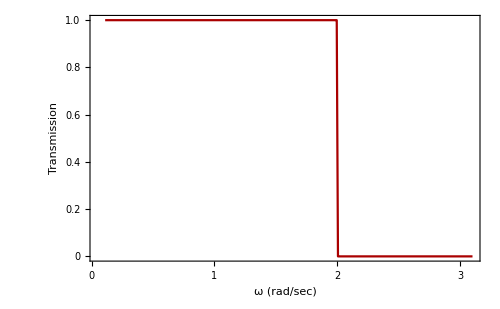

```mathematica
(****************************************** Parameters ********************************)
mChannel =1(*.12*); mSource=1(*.047*); mDrain=mSource;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;

kVerticalChannel = 1;kHorizontalChannel = 1(*13.7*);
kVerticalSource=1;kHorizontalSource= 1(*16.9*);
kVerticalDrain=kVerticalSource; kHorizontalDrain=kHorizontalSource;
kSC =1. (*15.3*)(*(kHorizontalChannel+kHorizontalSource)/2*); kCD = kSC (*(kHorizontalChannel+kHorizontalDrain)/2*);
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,2}];

(****************************************** dynamical Matrix ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
KChannel = Table[If[r==c,If[(MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]]) || (MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]]),kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@latticeCoordinates},{c, 1, Length@latticeCoordinates}];

(**********************************Couplings******************************************)
cSource = Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
cDrain = cSource;

(**********************************Leads******************************************)
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalSource],If[MemberQ[NNHI[[r,2]],c],-kHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
αDrain=Table[If[r==c,If[latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalDrain],If[MemberQ[NNHI[[r,2]],c],-kHorizontalDrain,0]],{r, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]},{c, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]}];

βSource=Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
βDrain=βSource;

Map[MatrixForm,{KChannel,cSource,αSource,αDrain,βSource}];

(************************************ Transmission Calculation ********************************************)
transmission=ParallelTable[
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSource ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mDrain ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.βDrain.GS11.ConjugateTranspose[βDrain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}]];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(Length@surfaceElements1-1),cDrain.Partition[Values[sol],{Length@cDrain}].ConjugateTranspose[cDrain],0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[(mChannel IdentityMatrix[Length@KChannel] ω1^2 - KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.11,3.1,.005}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

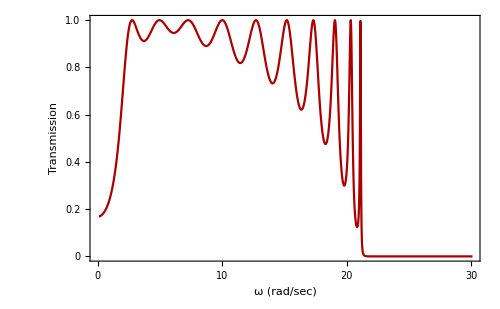

```mathematica
Map[MatrixForm,{ΓS,ΓD}];
```

## Graphene (hopping generated from geometry)

### Zigzag

#### Model

```mathematica
(********************************************* Function to generate spring between two points *********************************************)
generateSpring[p1_,p2_,turns_,springRadius_,tubeRadius_]:=Module[{vector,length,direction,helixPath,alignmentMatrix},
vector=p2-p1;
length=Norm[vector];
(*Handle the degenerate case where the points coincide*)
If[length==0,Return[Graphics3D[]]];
direction=vector/length;(*Normalize the direction vector*)
helixPath=Table[{springRadius Cos[2 Pi turns z/length],springRadius Sin[2 Pi turns z/length],z},{z,0,length,0.01}];(* helical path along the z-axis*)
alignmentMatrix=RotationMatrix3D[VectorAngle[{0,0,1},direction],Cross[{0,0,1},direction]];
helixPath=Map[alignmentMatrix.#+p1&,helixPath];(*Apply the alignment and translate the helix to p1*)
Graphics3D[{Black,Tube[helixPath,tubeRadius]}]];

(*Rotation matrix in 3D for a given axis and angle*)
RotationMatrix3D[angle_,axis_]:=Module[{c=Cos[angle],s=Sin[angle],v=1-Cos[angle],x,y,z},{x,y,z}=Normalize[axis];
{{x x v+c,x y v-z s,x z v+y s},{x y v+z s,y y v+c,y z v-x s},{x z v-y s,y z v+x s,z z v+c}}];

(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{(√3)/2,-1},{0,-1/2},{0,1/2},{(√3)/2,1}};
ax = {√3,0};
ay = {0,3};
nx=5; ny=2;
latticeCoordinates= supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

masses=Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[latticeCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@latticeCoordinates}],ViewPoint->Above,ImageSize->700];
springs=Show[Table[generateSpring[Append[hoppings[[i,1]],0],Append[hoppings[[i,2]],0],5,0.1,0.015],{i,1,Length@hoppings}]];
label = Show[Table[Graphics3D[Text[Style[i,20,White],Append[latticeCoordinates[[i]],0]]],{i,1,Length[latticeCoordinates]}]];
Show[masses,springs,label]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{2,5}},{2,{1,6}},{3,{4,7}},{4,{3,8}},{5,{1,9}},{6,{2,7,10}},{7,{3,6,11}},{8,{4,12}},{9,{5,10,13}},{10,{6,9,14}},{11,{7,12,15}},{12,{8,11,16}},{13,{9,17}},{14,{10,15,18}},{15,{11,14,19}},{16,{12,20}},{17,{13,18,21}},{18,{14,17,22}},{19,{15,20,23}},{20,{16,19,24}},{21,{17,25}},{22,{18,23,26}},{23,{19,22,27}},{24,{20,28}},{25,{21,26,29}},{26,{22,25,30}},{27,{23,28,31}},{28,{24,27,32}},{29,{25,33}},{30,{26,31,34}},{31,{27,30,35}},{32,{28,36}},{33,{29,34,37}},{34,{30,33,38}},{35,{31,36,39}},{36,{32,35,40}},{37,{33}},{38,{34,39}},{39,{35,38}},{40,{36}}}

#### Transmission

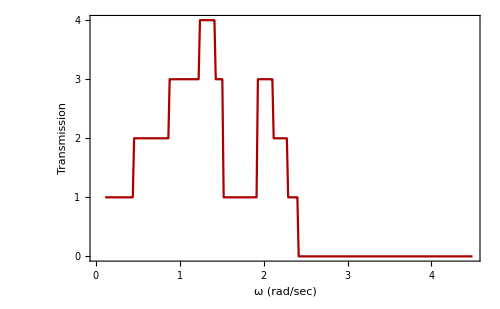

```mathematica
(****************************************** Parameters ********************************)
mChannel =1(*.12*); mSource=1(*.047*); mDrain=mSource;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;

kVerticalChannel = 1;kHorizontalChannel = 1.(*13.7*);
kVerticalSource=1;kHorizontalSource= 1.(*15.3*);
kVerticalDrain=kVerticalSource; kHorizontalDrain=kHorizontalSource;
kSC =1. (*15.3*)(*(kHorizontalChannel+kHorizontalSource)/2*); kCD = kSC (*(kHorizontalChannel+kHorizontalDrain)/2*);
η=0.000001;
surfaceElements1=Sort@Table[i,{i,1,8}];

(****************************************** dynamical Matrix ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
KChannel = Table[If[r==c,If[(MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]]) || (MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]]),kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@latticeCoordinates},{c, 1, Length@latticeCoordinates}];

(**********************************Couplings******************************************)
cSource = Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
cDrain = cSource;

(**********************************Leads******************************************)
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
αDrain= αSource;

βSource=Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}];
βDrain=βSource;

Map[MatrixForm,{KChannel,cSource,αSource,βSource}];

(************************************ Transmission Calculation ********************************************)
transmission=ParallelTable[
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSC ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mCD ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.βDrain.GS11.ConjugateTranspose[βDrain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}]];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(Length@surfaceElements1-1),cDrain.Partition[Values[sol],{Length@cDrain}].ConjugateTranspose[cDrain],0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[(mChannel IdentityMatrix[Length@KChannel] ω1^2 - KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.11,4.5,.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

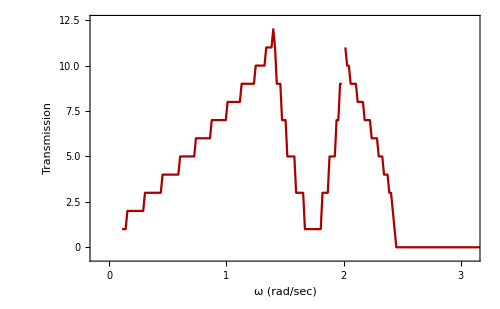

```mathematica
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->{{-0.1,3.1},{-0.5,12.5}},PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

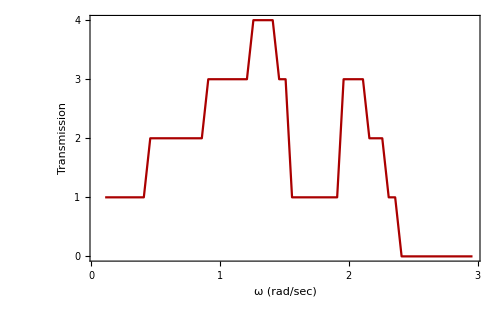

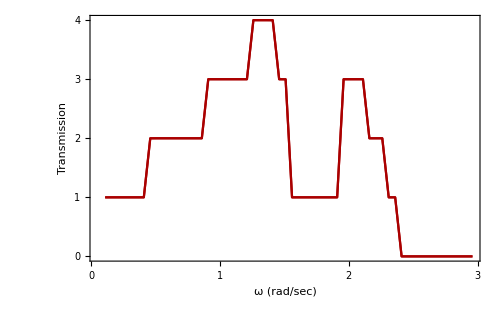

```mathematica
Show[%393,%394]
```

### Armchair

#### Model

```mathematica
(********************************************* Function to generate spring between two points *********************************************)
generateSpring[p1_,p2_,turns_,springRadius_,tubeRadius_]:=Module[{vector,length,direction,helixPath,alignmentMatrix},
vector=p2-p1;
length=Norm[vector];
(*Handle the degenerate case where the points coincide*)
If[length==0,Return[Graphics3D[]]];
direction=vector/length;(*Normalize the direction vector*)
helixPath=Table[{springRadius Cos[2 Pi turns z/length],springRadius Sin[2 Pi turns z/length],z},{z,0,length,0.01}];(* helical path along the z-axis*)
alignmentMatrix=RotationMatrix3D[VectorAngle[{0,0,1},direction],Cross[{0,0,1},direction]];
helixPath=Map[alignmentMatrix.#+p1&,helixPath];(*Apply the alignment and translate the helix to p1*)
Graphics3D[{Black,Tube[helixPath,tubeRadius]}]];

(*Rotation matrix in 3D for a given axis and angle*)
RotationMatrix3D[angle_,axis_]:=Module[{c=Cos[angle],s=Sin[angle],v=1-Cos[angle],x,y,z},{x,y,z}=Normalize[axis];
{{x x v+c,x y v-z s,x z v+y s},{x y v+z s,y y v+c,y z v-x s},{x z v-y s,y z v+x s,z z v+c}}];

(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}};
ax = {3,0};
ay = {0,√3};
nx=3; ny=3;
latticeCoordinates= supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

masses=Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[latticeCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@latticeCoordinates}],ViewPoint->Above,ImageSize->700];
springs=Show[Table[generateSpring[Append[hoppings[[i,1]],0],Append[hoppings[[i,2]],0],5,0.1,0.015],{i,1,Length@hoppings}]];
label = Show[Table[Graphics3D[Text[Style[i,20,White],Append[latticeCoordinates[[i]],0]]],{i,1,Length[latticeCoordinates]}]];
Show[masses,springs,label]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{4,5}},{2,{5,6}},{3,{6}},{4,{1,7}},{5,{1,2,8}},{6,{2,3,9}},{7,{4,10}},{8,{5,10,11}},{9,{6,11,12}},{10,{7,8,13}},{11,{8,9,14}},{12,{9,15}},{13,{10,16,17}},{14,{11,17,18}},{15,{12,18}},{16,{13,19}},{17,{13,14,20}},{18,{14,15,21}},{19,{16,22}},{20,{17,22,23}},{21,{18,23,24}},{22,{19,20,25}},{23,{20,21,26}},{24,{21,27}},{25,{22,28,29}},{26,{23,29,30}},{27,{24,30}},{28,{25,31}},{29,{25,26,32}},{30,{26,27,33}},{31,{28,34}},{32,{29,34,35}},{33,{30,35,36}},{34,{31,32}},{35,{32,33}},{36,{33}}}

#### Transmission

{1,2,3,4,5,6,7,8,9,10,11,12,25,26,27,28,29,30,31,32,33,34,35,36}

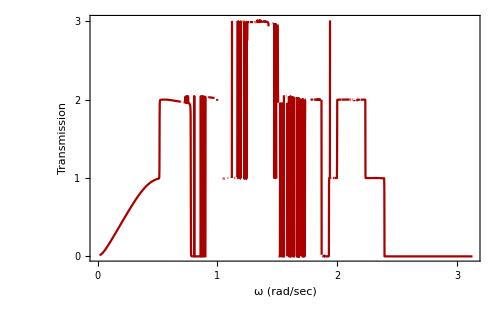

```mathematica
(****************************************** Parameters ********************************)
mChannel =1(*.12*); mSource=1(*.047*); mDrain=mSource;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;

kVerticalChannel = 1;kHorizontalChannel = 1(*13.7*);
kVerticalSource=1;kHorizontalSource= 1(*15.3*);
kVerticalDrain=kVerticalSource; kHorizontalDrain=kHorizontalSource;
kSC =1 (*15.3*)(*(kHorizontalChannel+kHorizontalSource)/2*); kCD = kSC (*(kHorizontalChannel+kHorizontalDrain)/2*);
η=0.001;
surfaceElements1=Sort@Table[i,{i,1,12}];

(****************************************** dynamical Matrix ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]]
KChannel = Table[If[r==c,If[(MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]]) || (MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]]),kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@latticeCoordinates},{c, 1, Length@latticeCoordinates}];

(**********************************Couplings******************************************)
cSource = Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
cDrain = cSource;

(**********************************Leads******************************************)
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalSource],If[MemberQ[NNHI[[r,2]],c],-kHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
αDrain= Table[If[r==c,If[latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalDrain,Length@NNHI[[r,2]]*kHorizontalDrain],If[MemberQ[NNHI[[r,2]],c],-kHorizontalDrain,0]],{r, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]},{c, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]}];

βSource=Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}];
βDrain=βSource;

Map[MatrixForm,{KChannel,cSource,αSource,βSource}];

(************************************ Transmission Calculation ********************************************)
transmission=ParallelTable[
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSource ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}],PrecisionGoal->4,MaxIterations->10000];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mDrain ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.βDrain.GS11.ConjugateTranspose[βDrain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}],PrecisionGoal->4,MaxIterations->10000];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(Length@surfaceElements1-1),cDrain.Partition[Values[sol],{Length@cDrain}].ConjugateTranspose[cDrain],0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[((mChannel*IdentityMatrix[Length@KChannel] ω1^2 +ⅈ η)- KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.017,3.13,.00137}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

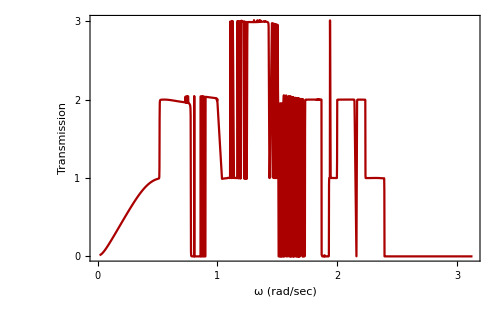

```mathematica
transmission =Select[transmission,Im[#[[2]]]==0&];
tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

```mathematica
transmission
```

{{0.017,0},{0.0301,0},{0.0432,0},{0.0563,0},{0.0694,0},{0.0825,0},{0.0956,0},{0.1087,0},{0.1218,0},{0.1349,0},{0.148,0},{0.1611,0},{0.1742,0},{0.1873,0},{0.2004,0},{0.2135,0},{0.2266,0},{0.2397,0},{0.2528,0},{0.2659,0},{0.279,0},{0.2921,0},{0.3052,0},{0.3183,0},{0.3314,0},{0.3445,0},{0.3576,0},{0.3707,0},{0.3838,0},{0.3969,0},{0.41,0},{0.4231,0},{0.4362,0},{0.4493,0},{0.4624,0},{0.4755,0},{0.4886,0},{0.5017,0},{0.5148,0},{0.5279,0},{0.541,0},{0.5541,0},{0.5672,0},{0.5803,0},{0.5934,0},{0.6065,0},{0.6196,0},{0.6327,0},{0.6458,0},{0.6589,0},{0.672,0},{0.6851,0},{0.6982,0},{0.7113,0},{0.7244,0},{0.7375,0},{0.7506,0},{0.7637,0},{0.7768,0},{0.7899,0},{0.803,0},{0.8161,0},{0.8292,0},{0.8423,0},{0.8554,0},{0.8685,0},{0.8816,0},{0.8947,0},{0.9078,0},{0.9209,0},{0.934,0},{0.9471,0},{0.9602,0},{0.9733,0},{0.9864,0},{0.9995,0},{1.0126,0},{1.0257,0},{1.0388,0},{1.0519,0},{1.065,0},{1.0781,0},{1.0912,0},{1.1043,0},{1.1174,0},{1.1305,0},{1.1436,1.18454×10^-10},{1.1567,7.84825×10^-10},{1.1698,3.02891×10^-9},{1.1829,2.06084×10^-10},{1.196,0},{1.2091,0},{1.2222,0},{1.2353,0},{1.2484,0},{1.2615,0},{1.2746,0},{1.2877,0},{1.3008,0},{1.3139,0},{1.327,0},{1.3401,0},{1.3532,0},{1.3663,0},{1.3794,0},{1.3925,0},{1.4056,0},{1.4187,0},{1.4318,0},{1.4449,0},{1.458,0},{1.4711,0},{1.4842,0},{1.4973,0},{1.5104,0},{1.5235,0},{1.5366,0},{1.5497,0},{1.5628,0},{1.5759,0},{1.589,0},{1.6021,0.0296618},{1.6152,0.13468},{1.6283,0.227358},{1.6414,0.30935},{1.6545,0.382056},{1.6676,0.446665},{1.6807,0.504188},{1.6938,0.555493},{1.7069,0.601327},{1.72,0.642333},{1.7331,0.679069},{1.7462,0.712018},{1.7593,0.741603},{1.7724,0.768193},{1.7855,0.792111},{1.7986,0.813641},{1.8117,0.833034},{1.8248,0.85051},{1.8379,0.866266},{1.851,0.880474},{1.8641,0.89329},{1.8772,0.90485},{1.8903,0.915278},{1.9034,0.924682},{1.9165,0.93316},{1.9296,0.940802},{1.9427,0.947685},{1.9558,0.953881},{1.9689,0.959454},{1.982,0.964461},{1.9951,0.968954},{2.0082,0.972981},{2.0213,0.976584},{2.0344,0.979802},{2.0475,0.982669},{2.0606,0.985218},{2.0737,0.987478},{2.0868,0.989473},{2.0999,0.99123},{2.113,0.992768},{2.1261,0.994108},{2.1392,0.995268},{2.1523,0.996265},{2.1654,0.997113},{2.1785,0.997826},{2.1916,0.998417},{2.2047,0.998897},{2.2178,0.999277},{2.2309,0.999565},{2.244,0.999772},{2.2571,0.999905},{2.2702,0.999971},{2.2833,0.999977},{2.2964,0.999929},{2.3095,0.999833},{2.3226,0.999693},{2.3357,0.999515},{2.3488,0.999303},{2.3619,0.99906},{2.375,0.998791},{2.3881,0.998498},{2.4012,0.998185},{2.4143,0.997854},{2.4274,0.997507},{2.4405,0.997148},{2.4536,0.996778},{2.4667,0.996398},{2.4798,0.996011},{2.4929,0.995618},{2.506,0.995221},{2.5191,0.99482},{2.5322,0.994417},{2.5453,0.994013},{2.5584,0.993609},{2.5715,0.993206},{2.5846,0.992804},{2.5977,0.992404},{2.6108,0.992007},{2.6239,0.991613},{2.637,0.991223},{2.6501,0.990837},{2.6632,0.990455},{2.6763,0.990078},{2.6894,0.989706},{2.7025,0.98934},{2.7156,0.988979},{2.7287,0.988624},{2.7418,0.988275},{2.7549,0.987932},{2.768,0.987595},{2.7811,0.987264},{2.7942,0.98694},{2.8073,1.18193},{2.8204,1.36661},{2.8335,1.49043},{2.8466,1.57876},{2.8597,1.64464},{2.8728,1.69543},{2.8859,1.73562},{2.899,1.76809},{2.9121,1.79478},{2.9252,1.81704},{2.9383,1.83583},{2.9514,1.85186},{2.9645,1.86566},{2.9776,1.87764},{2.9907,1.88811},{3.0038,1.89733},{3.0169,1.90548},{3.03,1.91274},{3.0431,1.91923},{3.0562,1.92505},{3.0693,1.9303},{3.0824,1.93504},{3.0955,1.93934},{3.1086,1.94325},{3.1217,1.94681},{3.1348,1.95007},{3.1479,1.95304},{3.161,1.95577},{3.1741,1.95826},{3.1872,1.96055},{3.2003,1.96266},{3.2134,1.96458},{3.2265,1.96635},{3.2396,1.96797},{3.2527,1.96945},{3.2658,1.97081},{3.2789,1.97204},{3.292,1.97316},{3.3051,1.97418},{3.3182,1.97509},{3.3313,1.97592},{3.3444,1.97665},{3.3575,1.9773},{3.3706,1.97786},{3.3837,1.97836},{3.3968,1.97878},{3.4099,1.97913},{3.423,1.97941},{3.4361,1.97963},{3.4492,1.97979},{3.4623,1.9799},{3.4754,1.97995},{3.4885,1.97995},{3.5016,1.9799},{3.5147,1.97981},{3.5278,1.97967},{3.5409,1.97949},{3.554,1.97928},{3.5671,1.97902},{3.5802,1.97874},{3.5933,1.97842},{3.6064,1.97807},{3.6195,1.97769},{3.6326,1.97729},{3.6457,1.97687},{3.6588,1.97643},{3.6719,1.97597},{3.685,1.97549},{3.6981,1.975},{3.7112,1.9745},{3.7243,1.97399},{3.7374,1.97347},{3.7505,1.97295},{3.7636,1.97242},{3.7767,1.97189},{3.7898,1.97136},{3.8029,1.97083},{3.816,1.9703},{3.8291,1.96978},{3.8422,1.96927},{3.8553,1.96877},{3.8684,1.96827},{3.8815,1.96779},{3.8946,1.96732},{3.9077,1.96687},{3.9208,1.96643},{3.9339,1.96601},{3.947,1.96561},{3.9601,1.96522},{3.9732,1.96486},{3.9863,1.96452},{3.9994,1.9642},{4.0125,1.9639},{4.0256,1.96363},{4.0387,1.96338},{4.0518,1.96316},{4.0649,1.96297},{4.078,1.9628},{4.0911,1.96266},{4.1042,1.96254},{4.1173,1.96245},{4.1304,1.9624},{4.1435,1.96236},{4.1566,1.96236},{4.1697,1.96239},{4.1828,1.96244},{4.1959,1.96252},{4.209,1.96263},{4.2221,1.96277},{4.2352,1.96294},{4.2483,1.96313},{4.2614,1.96335},{4.2745,1.96359},{4.2876,1.96386},{4.3007,1.96416},{4.3138,1.96448},{4.3269,1.96482},{4.34,1.96519},{4.3531,1.96557},{4.3662,1.96598},{4.3793,1.96641},{4.3924,1.96686},{4.4055,1.96732},{4.4186,1.96781},{4.4317,1.9683},{4.4448,1.96882},{4.4579,1.96934},{4.471,1.96988},{4.4841,1.97043},{4.4972,1.97099},{4.5103,1.97155},{4.5234,1.97213},{4.5365,1.97271},{4.5496,1.97329},{4.5627,1.97387},{4.5758,1.97446},{4.5889,1.97504},{4.602,1.97636},{4.6151,1.97794},{4.6282,1.97958},{4.6413,1.98127},{4.6544,1.98301},{4.6675,1.98482},{4.6806,1.98668},{4.6937,1.98861},{4.7068,1.99061},{4.7199,1.99269},{4.733,1.99486},{4.7461,1.99711},{4.7592,1.99946},{4.7723,2.00191},{4.7854,2.00447},{4.7985,2.00716},{4.8116,2.00998},{4.8247,2.01295},{4.8378,2.01608},{4.8509,2.01938},{4.864,2.02287},{4.8771,2.02656},{4.8902,2.03048},{4.9033,2.03464},{4.9164,2.03908},{4.9295,2.0438},{4.9426,2.04885},{4.9557,2.05425},{4.9688,2.06003},{4.9819,2.06623},{4.995,2.07288},{5.0081,2.08004},{5.0212,2.08773},{5.0343,2.09602},{5.0474,2.10496},{5.0605,2.1146},{5.0736,2.125},{5.0867,2.13622},{5.0998,2.14834},{5.1129,2.16143},{5.126,2.17554},{5.1391,2.19078},{5.1522,2.20719},{5.1653,2.22487},{5.1784,2.24388},{5.1915,2.26429},{5.2046,2.28616},{5.2177,2.30954},{5.2308,2.33445},{5.2439,2.36091},{5.257,2.38891},{5.2701,2.4184},{5.2832,2.44929},{5.2963,2.48147},{5.3094,2.51477},{5.3225,2.54896},{5.3356,2.58379},{5.3487,2.61894},{5.3618,2.65405},{5.3749,2.68872},{5.388,2.72253},{5.4011,2.75505},{5.4142,2.78585},{5.4273,2.81453},{5.4404,2.84072},{5.4535,2.86412},{5.4666,2.88448},{5.4797,2.90166},{5.4928,2.91556},{5.5059,2.9262},{5.519,2.93365},{5.5321,2.93805},{5.5452,2.9396},{5.5583,2.93853},{5.5714,2.93512},{5.5845,2.92965},{5.5976,2.92239},{5.6107,2.91365},{5.6238,2.90368},{5.6369,2.89274},{5.65,2.88107},{5.6631,2.86888},{5.6762,2.85635},{5.6893,2.84366},{5.7024,2.83094},{5.7155,2.81833},{5.7286,2.80592},{5.7417,2.79381},{5.7548,2.78206},{5.7679,2.77074},{5.781,2.75989},{5.7941,2.74956},{5.8072,2.73976},{5.8203,2.73053},{5.8334,2.72189},{5.8465,2.71383},{5.8596,2.70638},{5.8727,2.69953},{5.8858,2.69329},{5.8989,2.68766},{5.912,2.68263},{5.9251,2.6782},{5.9382,2.67437},{5.9513,2.67113},{5.9644,2.66847},{5.9775,2.66639},{5.9906,2.66488},{6.0037,2.66394},{6.0168,2.66356},{6.0299,2.66372},{6.043,2.66443},{6.0561,2.66568},{6.0692,2.66746},{6.0823,2.66976},{6.0954,2.67257},{6.1085,2.67589},{6.1216,2.67971},{6.1347,2.68402},{6.1478,2.68882},{6.1609,2.69408},{6.174,2.6998},{6.1871,2.70598},{6.2002,2.7126},{6.2133,2.71964},{6.2264,2.72709},{6.2395,2.73494},{6.2526,2.74317},{6.2657,2.75176},{6.2788,2.76069},{6.2919,2.76994},{6.305,2.77949},{6.3181,2.78929},{6.3312,2.79933},{6.3443,2.80958},{6.3574,2.81999},{6.3705,2.83052},{6.3836,2.84114},{6.3967,2.85179},{6.4098,2.86244},{6.4229,2.87301},{6.436,2.88347},{6.4491,2.89374},{6.4622,2.90377},{6.4753,2.91349},{6.4884,2.92283},{6.5015,2.93176},{6.5146,2.94025},{6.5277,2.94848},{6.5408,2.95532},{6.5539,2.96131},{6.567,2.9664},{6.5801,2.97051},{6.5932,2.97357},{6.6063,2.9755},{6.6194,2.97624},{6.6325,2.97571},{6.6456,2.97386},{6.6587,2.97063},{6.6718,2.96597},{6.6849,2.95983},{6.698,2.95219},{6.7111,2.94301},{6.7242,2.93228},{6.7373,2.91999},{6.7504,2.90612},{6.7635,2.89068},{6.7766,2.87368},{6.7897,2.85512},{6.8028,2.83502},{6.8159,2.81339},{6.829,2.79024},{6.8421,2.76558},{6.8552,2.73942},{6.8683,2.71176},{6.8814,2.68258},{6.8945,2.65186},{6.9076,2.61956},{6.9207,2.58564},{6.9338,2.55001},{6.9469,2.51257},{6.96,2.47321},{6.9731,2.43176},{6.9862,2.38802},{6.9993,2.34175},{7.0124,2.29266},{7.0255,2.24037},{7.0386,2.18445},{7.0517,2.12435},{7.0648,2.05941},{7.0779,1.98881},{7.091,1.91155},{7.1041,1.82634},{7.1172,1.73156},{7.1303,1.62511},{7.1434,1.50423},{7.1565,1.23323},{7.1696,1.04565},{7.1827,0.825368},{7.1958,0.565444},{7.2089,0.262403},{7.222,0.0282772},{7.2351,0.00668398},{7.2482,0.0000625143},{7.2613,0.0105114},{7.2744,0.0811015},{7.2875,0.33117},{7.3006,0.778666},{7.3137,0.166323},{7.3268,0.194596},{7.3399,0.226717},{7.353,0.262983},{7.3661,0.303537},{7.3792,0.348272},{7.3923,0.396703},{7.4054,0.4478},{7.4185,0.499775},{7.4316,0.549762},{7.4447,0.59314},{7.4578,0.621599},{7.4709,0.615923},{7.484,0.511587},{7.4971,0.0884529},{7.5102,0.50205},{7.5233,0.854687},{7.5364,0.91312},{7.5495,0.921363},{7.5626,0.914728},{7.5757,0.90132},{7.5888,0.884243},{7.6019,0.865226},{7.615,0.845433},{7.6281,0.825705},{7.6412,0.806664},{7.6543,0.819867},{7.6674,0.794125},{7.6805,0.769587},{7.6936,0.837675},{7.7067,1.01246},{7.7198,1.16335},{7.7329,1.1363},{7.746,1.20837},{7.7591,1.26648},{7.7722,1.31278},{7.7853,1.34894},{7.7984,1.37617},{7.8115,1.39541},{7.8246,1.40726},{7.8377,1.41213},{7.8508,1.41017},{7.8639,1.4013},{7.877,1.3852},{7.8901,1.36124},{7.9032,1.32841},{7.9163,1.28521},{7.9294,1.2294},{7.9425,1.15769},{7.9556,1.06511},{7.9687,0.943878},{7.9818,0.891557},{7.9949,0.90191},{8.008,0.911467},{8.0211,0.920292},{8.0342,0.928442},{8.0473,0.935969},{8.0604,0.942916},{8.0735,0.949325},{8.0866,0.95523},{8.0997,0.960663},{8.1128,0.965652},{8.1259,0.970222},{8.139,0.974396},{8.1521,0.978193},{8.1652,0.981633},{8.1783,0.984731},{8.1914,0.987501},{8.2045,0.989959},{8.2176,0.992114},{8.2307,0.99398},{8.2438,0.995565},{8.2569,0.996879},{8.27,0.997931},{8.2831,0.998729},{8.2962,0.999281},{8.3093,0.999593},{8.3224,0.999673},{8.3355,0.999527},{8.3486,0.999161},{8.3617,0.998581},{8.3748,0.997794},{8.3879,0.996806},{8.401,0.995621},{8.4141,0.994248},{8.4272,0.99269},{8.4403,0.990954},{8.4534,0.989047},{8.4665,0.986975},{8.4796,0.984743},{8.4927,0.982358},{8.5058,0.979826},{8.5189,0.977155},{8.532,0.974351},{8.5451,0.971421},{8.5582,0.968371},{8.5713,0.96521},{8.5844,0.961944},{8.5975,0.958581},{8.6106,0.955128},{8.6237,0.951593},{8.6368,0.947984},{8.6499,0.944308},{8.663,0.940574},{8.6761,0.936789},{8.6892,0.932961},{8.7023,0.929099},{8.7154,0.92521},{8.7285,0.921303},{8.7416,0.917385},{8.7547,0.913465},{8.7678,0.90955},{8.7809,0.905649},{8.794,0.90177},{8.8071,0.897919},{8.8202,0.894106},{8.8333,0.890338},{8.8464,0.886622},{8.8595,0.882966},{8.8726,0.879378},{8.8857,0.875864},{8.8988,0.872433},{8.9119,0.86909},{8.925,0.865843},{8.9381,0.8627},{8.9512,0.859666},{8.9643,0.856748},{8.9774,0.853953},{8.9905,0.851287},{9.0036,0.848756},{9.0167,0.846367},{9.0298,0.844125},{9.0429,0.842036},{9.056,0.840107},{9.0691,0.838342},{9.0822,0.836747},{9.0953,0.835328},{9.1084,0.834089},{9.1215,0.833037},{9.1346,0.832175},{9.1477,0.831509},{9.1608,0.831044},{9.1739,0.830783},{9.187,0.830733},{9.2001,0.830896},{9.2132,0.831277},{9.2263,0.83188},{9.2394,0.832708},{9.2525,0.833766},{9.2656,0.835056},{9.2787,0.836581},{9.2918,0.838344},{9.3049,0.840347},{9.318,0.842592},{9.3311,0.845081},{9.3442,0.847813},{9.3573,0.850791},{9.3704,0.854012},{9.3835,0.857477},{9.3966,0.861183},{9.4097,0.865127},{9.4228,0.869305},{9.4359,0.873713},{9.449,0.878343},{9.4621,0.883188},{9.4752,0.888239},{9.4883,0.893484},{9.5014,0.89891},{9.5145,0.904502},{9.5276,0.910241},{9.5407,0.916107},{9.5538,0.922078},{9.5669,0.928126},{9.58,0.934222},{9.5931,0.940334},{9.6062,0.946425},{9.6193,0.952454},{9.6324,0.958377},{9.6455,0.964146},{9.6586,0.969707},{9.6717,0.975005},{9.6848,0.979978},{9.6979,0.984562},{9.711,0.988689},{9.7241,0.992287},{9.7372,0.995282},{9.7503,0.997597},{9.7634,0.999157},{9.7765,0.999882},{9.7896,0.999696},{9.8027,0.998524},{9.8158,0.996295},{9.8289,0.992942},{9.842,0.988403},{9.8551,0.982626},{9.8682,0.975566},{9.8813,0.967189},{9.8944,0.957473},{9.9075,0.946406},{9.9206,0.933992},{9.9337,0.920245},{9.9468,0.905196},{9.9599,0.888885},{9.973,0.871367},{9.9861,0.852709},{9.9992,0.833341},{10.0123,0.813308},{10.0254,0.792383},{10.0385,0.770663},{10.0516,0.748245},{10.0647,0.725229},{10.0778,0.701712},{10.0909,0.677788},{10.104,0.653543},{10.1171,0.629058},{10.1302,0.604402},{10.1433,0.57963},{10.1564,0.554777},{10.1695,0.529849},{10.1826,0.504793},{10.1957,0.449104},{10.2088,0.437252},{10.2219,0.429279},{10.235,0.411146},{10.2481,0.391638},{10.2612,0.357804},{10.2743,0.33721},{10.2874,0.316474},{10.3005,0.29543},{10.3136,0.273907},{10.3267,0.251723},{10.3398,0.228676},{10.3529,0.204533},{10.366,0.179026},{10.3791,0.151843},{10.3922,0.122613},{10.4053,0.0908976},{10.4184,0.0561616},{10.4315,0.0363848},{10.4446,0.034442},{10.4577,0.0317949},{10.4708,0.0284646},{10.4839,0.0244926},{10.497,0.029408},{10.5101,0.0244394},{10.5232,0.0184002},{10.5363,0.0110192},{10.5494,-0.00297307},{10.5625,-0.0362056},{10.5756,-0.0604335},{10.5887,-0.084335},{10.6018,0.0324438},{10.6149,0.0351316},{10.628,0.0375374},{10.6411,0.0397456},{10.6542,0.041805},{10.6673,0.0437448},{10.6804,0.0455827},{10.6935,0.0473285},{10.7066,0.0489866},{10.7197,0.0505578},{10.7328,0.0520394},{10.7459,0.0534264},{10.759,0.0547115},{10.7721,0.0558854},{10.7852,0.0569367},{10.7983,0.0578522},{10.8114,0.0586164},{10.8245,0.0592119},{10.8376,0.0596185},{10.8507,0.059813},{10.8638,0.0597688},{10.8769,0.0594545},{10.89,0.0588323},{10.9031,0.0578559},{10.9162,0.0564654},{10.9293,0.0545797},{10.9424,0.0520808},{10.9555,0.0487773},{10.9686,0.0443069},{10.9817,0.0377479},{10.9948,0.0201666},{11.0079,0.0346641},{11.021,0.0427116},{11.0341,0.0495679},{11.0472,0.0558156},{11.0603,0.0616956},{11.0734,0.0673425},{11.0865,0.0728446},{11.0996,0.0782665},{11.1127,0.0836591},{11.1258,0.0890648},{11.1389,0.0945207},{11.152,0.10006},{11.1651,0.105715},{11.1782,0.111514},{11.1913,0.117486},{11.2044,0.12366},{11.2175,0.130065},{11.2306,0.13673},{11.2437,0.143683},{11.2568,0.150956},{11.2699,0.158579},{11.283,0.166583},{11.2961,0.175002},{11.3092,0.183866},{11.3223,0.193209},{11.3354,0.20306},{11.3485,0.213447},{11.3616,0.224393},{11.3747,0.235909},{11.3878,0.247994},{11.4009,0.260622},{11.414,0.273727},{11.4271,0.287179},{11.4402,0.300745},{11.4533,0.314004},{11.4664,0.3262},{11.4795,0.335922},{11.4926,0.340339},{11.5057,0.333123},{11.5188,0.297525},{11.5319,0.179076},{11.545,0.170193},{11.5581,0.962951},{11.5712,0.874387},{11.5843,0.845412},{11.5974,0.848477},{11.6105,0.866235},{11.6236,0.891254},{11.6367,0.919585},{11.6498,0.948614},{11.6629,0.976289},{11.676,1.00084},{11.6891,1.02068},{11.7022,1.03444},{11.7153,1.04103},{11.7284,1.03967},{11.7415,1.02997},{11.7546,1.01192},{11.7677,0.985898},{11.7808,0.952535},{11.7939,0.912654},{11.807,0.867129},{11.8201,0.816763},{11.8332,0.762165},{11.8463,0.703632},{11.8594,0.641025},{11.8725,0.573609},{11.8856,0.499834},{11.8987,0.416998},{11.9118,0.320849},{11.9249,0.205793},{11.938,0.0821565},{11.9511,0.000105596},{11.9642,0.212465},{11.9773,0.801297},{11.9904,0.980141},{12.0035,0.903001},{12.0166,0.802581},{12.0297,0.719248},{12.0428,0.653188},{12.0559,0.600173},{12.069,0.556706},{12.0821,0.520342},{12.0952,0.4894},{12.1083,0.462715},{12.1214,0.439457},{12.1345,0.419026},{12.1476,0.400984},{12.1607,0.385014},{12.1738,0.370904},{12.1869,0.358547},{12.2,0.347988},{12.2131,0.339549},{12.2262,0.334285},{12.2393,0.335978},{12.2524,0.368645},{12.2655,0.0733122},{12.2786,0.231152},{12.2917,0.243354},{12.3048,0.243185},{12.3179,0.239361},{12.331,0.233837},{12.3441,0.227187},{12.3572,0.219522},{12.3703,0.210723},{12.3834,0.200502},{12.3965,0.188392},{12.4096,0.173693},{12.4227,0.155355},{12.4358,0.13177},{12.4489,0.100373},{12.462,0.0568406},{12.4751,0},{12.4882,0},{12.5013,0},{12.5144,0},{12.5275,0},{12.5406,2.80974×10^-9},{12.5537,0},{12.5668,0},{12.5799,0},{12.593,0},{12.6061,0},{12.6192,0},{12.6323,0},{12.6454,0},{12.6585,0},{12.6716,0},{12.6847,0},{12.6978,0},{12.7109,0},{12.724,0},{12.7371,0},{12.7502,0},{12.7633,0},{12.7764,0},{12.7895,0},{12.8026,0},{12.8157,0},{12.8288,0},{12.8419,0},{12.855,0},{12.8681,0},{12.8812,0},{12.8943,0},{12.9074,0},{12.9205,0},{12.9336,0},{12.9467,0},{12.9598,0},{12.9729,0},{12.986,0},{12.9991,0},{13.0122,0},{13.0253,0},{13.0384,0},{13.0515,0},{13.0646,0},{13.0777,0},{13.0908,0},{13.1039,0},{13.117,0},{13.1301,0},{13.1432,0},{13.1563,0},{13.1694,0},{13.1825,0},{13.1956,0},{13.2087,0},{13.2218,0},{13.2349,0},{13.248,0},{13.2611,0},{13.2742,0},{13.2873,0},{13.3004,0},{13.3135,0},{13.3266,0},{13.3397,0},{13.3528,0},{13.3659,0},{13.379,0},{13.3921,0},{13.4052,0},{13.4183,0},{13.4314,0},{13.4445,0},{13.4576,0},{13.4707,0},{13.4838,0},{13.4969,0},{13.51,0},{13.5231,0},{13.5362,0},{13.5493,0},{13.5624,0},{13.5755,0},{13.5886,0},{13.6017,0},{13.6148,0},{13.6279,0},{13.641,0},{13.6541,0},{13.6672,0},{13.6803,0},{13.6934,0},{13.7065,0},{13.7196,0},{13.7327,0},{13.7458,0},{13.7589,0},{13.772,0},{13.7851,0},{13.7982,0},{13.8113,0},{13.8244,0},{13.8375,0},{13.8506,0},{13.8637,0},{13.8768,0},{13.8899,0},{13.903,0},{13.9161,0},{13.9292,0},{13.9423,0},{13.9554,0},{13.9685,0},{13.9816,0},{13.9947,0},{14.0078,0},{14.0209,0},{14.034,0},{14.0471,0},{14.0602,0},{14.0733,0},{14.0864,0},{14.0995,0},{14.1126,0},{14.1257,0},{14.1388,0},{14.1519,0},{14.165,0},{14.1781,0},{14.1912,0},{14.2043,0},{14.2174,0},{14.2305,0},{14.2436,0},{14.2567,0},{14.2698,0},{14.2829,0},{14.296,0},{14.3091,0},{14.3222,0},{14.3353,0},{14.3484,0},{14.3615,0},{14.3746,0},{14.3877,0},{14.4008,0},{14.4139,0},{14.427,0},{14.4401,0},{14.4532,0},{14.4663,0},{14.4794,0},{14.4925,0},{14.5056,0},{14.5187,0},{14.5318,0},{14.5449,0},{14.558,0},{14.5711,0},{14.5842,0},{14.5973,0},{14.6104,0},{14.6235,0},{14.6366,0},{14.6497,0},{14.6628,0},{14.6759,0},{14.689,0},{14.7021,0},{14.7152,0},{14.7283,0},{14.7414,0},{14.7545,0},{14.7676,0},{14.7807,0},{14.7938,0},{14.8069,0},{14.82,0},{14.8331,0},{14.8462,0},{14.8593,0},{14.8724,0},{14.8855,0},{14.8986,0},{14.9117,0},{14.9248,0},{14.9379,0},{14.951,0},{14.9641,0},{14.9772,0},{14.9903,0},{15.0034,0},{15.0165,0},{15.0296,0},{15.0427,0},{15.0558,0},{15.0689,0},{15.082,0},{15.0951,0},{15.1082,0},{15.1213,0}}

#### Transmission (inspect)

```mathematica
(****************************************** Parameters ********************************)
mChannel =.4(*.12*); mSource=.65(*.047*); mDrain=mSource;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;

kVerticalChannel = 1;kHorizontalChannel = 13.7(*13.7*);
kVerticalSource=1;kHorizontalSource= 15.3(*15.3*);
kVerticalDrain=kVerticalSource; kHorizontalDrain=kHorizontalSource;
kSC =14.1 (*15.3*)(*(kHorizontalChannel+kHorizontalSource)/2*); kCD = kSC (*(kHorizontalChannel+kHorizontalDrain)/2*);
η=0.000001;
surfaceElements1=Sort@Table[i,{i,1,8}];

(****************************************** dynamical Matrix ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]]
KChannel = Table[If[r==c,If[(MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]]) || (MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]]),kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@latticeCoordinates},{c, 1, Length@latticeCoordinates}];

(**********************************Couplings******************************************)
cSource = Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
cDrain = cSource;

(**********************************Leads******************************************)
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
αDrain= Table[If[r==c,If[latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]},{c, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]}];

βSource=Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}];
βDrain=βSource;

Map[MatrixForm,{KChannel,mChannel*IdentityMatrix[Length@KChannel],cSource,αSource,αDrain,βSource}]

(************************************ Transmission Calculation ********************************************)
ω1=10.5625;
(*transmission=ParallelTable[*)
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSC ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓS =Chop[-2Im[ΣS],0.0000001];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mCD ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.βDrain.GS11.ConjugateTranspose[βDrain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}]];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(Length@surfaceElements1-1),cDrain.Partition[Values[sol],{Length@cDrain}].ConjugateTranspose[cDrain],0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓD=Chop[-2Im[ΣD],0.0000001];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[((mChannel*IdentityMatrix[Length@KChannel] ω1^2 +ⅈ η)- KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
Chop[ Tr[ΓS.GR.ΓD.GA]]
(*{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.11,3,.0131}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]*)
Map[MatrixForm,{GR,ΣS,ΣD,ΓS,ΓD}]
```

{1,2,3,4,5,6,7,8,17,18,19,20,21,22,23,24}

{(41.5 | 0 | -13.7 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 27.8 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-13.7 | 0 | 27.4 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-13.7 | -13.7 | 0 | 41.1 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -13.7 | 0 | 27.4 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -13.7 | 0 | 41.1 | -13.7 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -13.7 | -13.7 | 41.1 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 27.4 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 41.1 | 0 | -13.7 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 27.4 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 27.4 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | -13.7 | 0 | 41.1 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 27.4 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 41.1 | -13.7 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | -13.7 | 41.1 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 27.4 | 0 | -13.7 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 41.1 | 0 | -13.7 | -13.7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 27.4 | 0 | -13.7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 27.4 | 0 | -13.7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | -13.7 | 0 | 41.1 | 0 | -13.7 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 27.4 | 0 | -13.7 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 41.1 | -13.7 | -13.7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | -13.7 | 41.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 27.8),(0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.4),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-14.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -14.1 | 0 | 0 | 0 | 0 | 0 | 0),(44.7 | 0 | -13.7 | -13.7 | 0 | 0 | 0 | 0
0 | 29.4 | 0 | -13.7 | 0 | 0 | 0 | 0
-13.7 | 0 | 27.4 | 0 | -13.7 | 0 | 0 | 0
-13.7 | -13.7 | 0 | 41.1 | 0 | -13.7 | 0 | 0
0 | 0 | -13.7 | 0 | 27.4 | 0 | -13.7 | 0
0 | 0 | 0 | -13.7 | 0 | 41.1 | -13.7 | -13.7
0 | 0 | 0 | 0 | -13.7 | -13.7 | 41.1 | 0
0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 27.4),(41.1 | 0 | -13.7 | -13.7 | 0 | 0 | 0 | 0
0 | 27.4 | 0 | -13.7 | 0 | 0 | 0 | 0
-13.7 | 0 | 27.4 | 0 | -13.7 | 0 | 0 | 0
-13.7 | -13.7 | 0 | 41.1 | 0 | -13.7 | 0 | 0
0 | 0 | -13.7 | 0 | 27.4 | 0 | -13.7 | 0
0 | 0 | 0 | -13.7 | 0 | 41.1 | -13.7 | -13.7
0 | 0 | 0 | 0 | -13.7 | -13.7 | 44.7 | 0
0 | 0 | 0 | 0 | 0 | -13.7 | 0 | 29.4),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-14.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -14.1 | 0 | 0 | 0 | 0 | 0 | 0)}

0.0171538

{(-0.043872-0.00927977 ⅈ | 0.0354878-0.00235087 ⅈ | 0.0676544+0.00628966 ⅈ | -0.0190092+0.0151787 ⅈ | -0.0411976+0.00137107 ⅈ | 0.0132774+0.00772345 ⅈ | -0.015852-0.00801366 ⅈ | 0.0314434-0.00915314 ⅈ | 0.0320007-0.00703169 ⅈ | -0.0528148+0.00378583 ⅈ | -0.0273519+0.00543093 ⅈ | 0.0349666+0.00439278 ⅈ | 0.00239195+0.000202771 ⅈ | 0.0118132+0.00211509 ⅈ | 0.0243443-0.00568589 ⅈ | -0.0623517+0.000748658 ⅈ | -0.0204717-0.000854242 ⅈ | 0.0665887-0.00305647 ⅈ | 0.00230321+0.0028112 ⅈ | -0.0213778+0.00309458 ⅈ | 0.0175756-0.0026806 ⅈ | -0.0406141+0.00311412 ⅈ | -0.024403+0.000559421 ⅈ | 0.0562354-0.00445562 ⅈ
0.0354878-0.00235087 ⅈ | -0.092281-0.00288149 ⅈ | -0.106406+0.000449042 ⅈ | 0.139039+0.0058487 ⅈ | 0.0983083+0.00178624 ⅈ | 0.0210028+0.00372683 ⅈ | -0.0172083-0.00269509 ⅈ | -0.127237-0.00411295 ⅈ | -0.114881-0.00481932 ⅈ | 0.138986+0.00144484 ⅈ | 0.0943068+0.00163946 ⅈ | -0.0475265+0.00229618 ⅈ | -0.00370129+0.00275785 ⅈ | -0.0118709+0.00278341 ⅈ | -0.0896528-0.00510721 ⅈ | 0.140235+0.00209454 ⅈ | 0.03865-0.00422659 ⅈ | -0.164463-0.00541712 ⅈ | 0.0131414+0.00147818 ⅈ | 0.0665623+0.00471702 ⅈ | -0.0551742+0.00236791 ⅈ | 0.108678+0.00842949 ⅈ | 0.0562354-0.00445562 ⅈ | -0.150773-0.00243125 ⅈ
0.0676544+0.00628966 ⅈ | -0.106406+0.000449042 ⅈ | -0.0223051-0.00483588 ⅈ | 0.0706184-0.00928492 ⅈ | 0.033385-0.000208965 ⅈ | 0.0205733-0.00434864 ⅈ | -0.0196737+0.00509863 ⅈ | -0.0562405+0.00530569 ⅈ | -0.0488941+0.00324515 ⅈ | 0.0501443-0.0023228 ⅈ | 0.0390712-0.00354901 ⅈ | -0.0068116-0.00238496 ⅈ | -0.000234644+0.00121743 ⅈ | 0.000503131-0.000308425 ⅈ | -0.0387762+0.0020182 ⅈ | 0.0454583+0.000446153 ⅈ | 0.00971302-0.00142851 ⅈ | -0.057663-0.000252573 ⅈ | 0.00922802-0.00152192 ⅈ | 0.0270479-0.000128564 ⅈ | -0.0213165+0.0033422 ⅈ | 0.0409875+0.00171418 ⅈ | 0.0175756-0.0026806 ⅈ | -0.0551742+0.00236791 ⅈ
-0.0190092+0.0151787 ⅈ | 0.139039+0.0058487 ⅈ | 0.0706184-0.00928492 ⅈ | -0.107189-0.0265832 ⅈ | -0.0697873-0.0035037 ⅈ | -0.0194447-0.0141845 ⅈ | 0.0171331+0.0136905 ⅈ | 0.0950616+0.016544 ⅈ | 0.0848217+0.0141641 ⅈ | -0.100087-0.00661815 ⅈ | -0.0697565-0.00911429 ⅈ | 0.0307892-0.00822226 ⅈ | 0.0028911-0.00270366 ⅈ | 0.00733976-0.00542942 ⅈ | 0.0661212+0.0125139 ⅈ | -0.0987998-0.00289404 ⅈ | -0.0272513+0.00491183 ⅈ | 0.116892+0.00906842 ⅈ | -0.0109241-0.00526956 ⅈ | -0.0481823-0.00850871 ⅈ | 0.0409875+0.00171418 ⅈ | -0.0772383-0.01179 ⅈ | -0.0406141+0.00311412 ⅈ | 0.108678+0.00842949 ⅈ
-0.0411976+0.00137107 ⅈ | 0.0983083+0.00178624 ⅈ | 0.033385-0.000208965 ⅈ | -0.0697873-0.0035037 ⅈ | -0.000781217-0.00110831 ⅈ | -0.0391465-0.00225541 ⅈ | 0.04059+0.00160257 ⅈ | 0.0392742+0.0024817 ⅈ | 0.0294793+0.0029512 ⅈ | -0.0102374-0.000865118 ⅈ | -0.0217768-0.000968354 ⅈ | -0.0264016-0.0013939 ⅈ | -0.0020969-0.00173358 ⅈ | -0.0124458-0.00172728 ⅈ | 0.0244135+0.00314818 ⅈ | 0.00519183-0.00130966 ⅈ | 0.00825838+0.00265047 ⅈ | 0.00591755+0.00337406 ⅈ | -0.0139066-0.000897519 ⅈ | -0.0126326-0.00293293 ⅈ | 0.00922802-0.00152192 ⅈ | -0.0109241-0.00526956 ⅈ | 0.00230321+0.0028112 ⅈ | 0.0131414+0.00147818 ⅈ
0.0132774+0.00772345 ⅈ | 0.0210028+0.00372683 ⅈ | 0.0205733-0.00434864 ⅈ | -0.0194447-0.0141845 ⅈ | -0.0391465-0.00225541 ⅈ | -0.0292748-0.007799 ⅈ | 0.02865+0.00718462 ⅈ | 0.0713231+0.00900745 ⅈ | 0.0610464+0.00820499 ⅈ | -0.0604078-0.00352708 ⅈ | -0.0489986-0.00472425 ⅈ | 0.00463444-0.00457245 ⅈ | 0.000565136-0.00226466 ⅈ | -0.00183164-0.00350091 ⅈ | 0.048288+0.00757186 ⅈ | -0.052451-0.00209824 ⅈ | -0.0111635+0.00381646 ⅈ | 0.0677842+0.00613926 ⅈ | -0.0126326-0.00293293 ⅈ | -0.0327818-0.00562135 ⅈ | 0.0270479-0.000128564 ⅈ | -0.0481823-0.00850871 ⅈ | -0.0213778+0.00309458 ⅈ | 0.0665623+0.00471702 ⅈ
-0.015852-0.00801366 ⅈ | -0.0172083-0.00269509 ⅈ | -0.0196737+0.00509863 ⅈ | 0.0171331+0.0136905 ⅈ | 0.04059+0.00160257 ⅈ | 0.02865+0.00718462 ⅈ | -0.0313647-0.00711372 ⅈ | 0.00685667-0.00842621 ⅈ | 0.0118264-0.00695602 ⅈ | -0.0372717+0.00341061 ⅈ | -0.0116888+0.00476663 ⅈ | 0.0400093+0.00413767 ⅈ | 0.00287132+0.000962399 ⅈ | 0.0151464+0.00248033 ⅈ | 0.0080784-0.00597676 ⅈ | -0.0519866+0.00120063 ⅈ | -0.0200972-0.00190423 ⅈ | 0.0502222-0.00399001 ⅈ | 0.00825838+0.00265047 ⅈ | -0.0111635+0.00381646 ⅈ | 0.00971302-0.00142851 ⅈ | -0.0272513+0.00491183 ⅈ | -0.0204717-0.000854242 ⅈ | 0.03865-0.00422659 ⅈ
0.0314434-0.00915314 ⅈ | -0.127237-0.00411295 ⅈ | -0.0562405+0.00530569 ⅈ | 0.0950616+0.016544 ⅈ | 0.0392742+0.0024817 ⅈ | 0.0713231+0.00900745 ⅈ | 0.00685667-0.00842621 ⅈ | -0.120278-0.0104364 ⅈ | -0.112362-0.00932013 ⅈ | 0.152908+0.00411545 ⅈ | 0.0940583+0.00556374 ⅈ | -0.0719914+0.0052616 ⅈ | -0.00590789+0.00232421 ⅈ | -0.0220147+0.00385027 ⅈ | -0.0866296-0.00848623 ⅈ | 0.164288+0.00223352 ⅈ | 0.0502222-0.00399001 ⅈ | -0.184563-0.00665873 ⅈ | 0.00591755+0.00337406 ⅈ | 0.0677842+0.00613926 ⅈ | -0.057663-0.000252573 ⅈ | 0.116892+0.00906842 ⅈ | 0.0665887-0.00305647 ⅈ | -0.164463-0.00541712 ⅈ
0.0320007-0.00703169 ⅈ | -0.114881-0.00481932 ⅈ | -0.0488941+0.00324515 ⅈ | 0.0848217+0.0141641 ⅈ | 0.0294793+0.0029512 ⅈ | 0.0610464+0.00820499 ⅈ | 0.0118264-0.00695602 ⅈ | -0.112362-0.00932013 ⅈ | -0.09357-0.00936562 ⅈ | 0.0802394+0.00351426 ⅈ | 0.0737843+0.00446561 ⅈ | 0.0114682+0.00490125 ⅈ | 0.000792652+0.0037505 ⅈ | 0.0103786+0.00458971 ⅈ | -0.074781-0.00918154 ⅈ | 0.0606412+0.00309884 ⅈ | 0.0080784-0.00597676 ⅈ | -0.0866296-0.00848623 ⅈ | 0.0244135+0.00314818 ⅈ | 0.048288+0.00757186 ⅈ | -0.0387762+0.0020182 ⅈ | 0.0661212+0.0125139 ⅈ | 0.0243443-0.00568589 ⅈ | -0.0896528-0.00510721 ⅈ
-0.0528148+0.00378583 ⅈ | 0.138986+0.00144484 ⅈ | 0.0501443-0.0023228 ⅈ | -0.100087-0.00661815 ⅈ | -0.0102374-0.000865118 ⅈ | -0.0604078-0.00352708 ⅈ | -0.0372717+0.00341061 ⅈ | 0.152908+0.00411545 ⅈ | 0.0802394+0.00351426 ⅈ | -0.131861-0.00164775 ⅈ | -0.0692715-0.00227167 ⅈ | 0.0858885-0.00204356 ⅈ | 0.00686352-0.000657836 ⅈ | 0.0295132-0.00134048 ⅈ | 0.0606412+0.00309884 ⅈ | -0.154127-0.000710227 ⅈ | -0.0519866+0.00120063 ⅈ | 0.164288+0.00223352 ⅈ | 0.00519183-0.00130966 ⅈ | -0.052451-0.00209824 ⅈ | 0.0454583+0.000446153 ⅈ | -0.0987998-0.00289404 ⅈ | -0.0623517+0.000748658 ⅈ | 0.140235+0.00209454 ⅈ
-0.0273519+0.00543093 ⅈ | 0.0943068+0.00163946 ⅈ | 0.0390712-0.00354901 ⅈ | -0.0697565-0.00911429 ⅈ | -0.0217768-0.000968354 ⅈ | -0.0489986-0.00472425 ⅈ | -0.0116888+0.00476663 ⅈ | 0.0940583+0.00556374 ⅈ | 0.0737843+0.00446561 ⅈ | -0.0692715-0.00227167 ⅈ | -0.000348831-0.00320883 ⅈ | -0.00695539-0.00270731 ⅈ | -0.000352964-0.000430789 ⅈ | -0.00272239-0.00149704 ⅈ | 0.000792652+0.0037505 ⅈ | 0.00686352-0.000657836 ⅈ | 0.00287132+0.000962399 ⅈ | -0.00590789+0.00232421 ⅈ | -0.0020969-0.00173358 ⅈ | 0.000565136-0.00226466 ⅈ | -0.000234644+0.00121743 ⅈ | 0.0028911-0.00270366 ⅈ | 0.00239195+0.000202771 ⅈ | -0.00370129+0.00275785 ⅈ
0.0349666+0.00439278 ⅈ | -0.0475265+0.00229618 ⅈ | -0.0068116-0.00238496 ⅈ | 0.0307892-0.00822226 ⅈ | -0.0264016-0.0013939 ⅈ | 0.00463444-0.00457245 ⅈ | 0.0400093+0.00413767 ⅈ | -0.0719914+0.0052616 ⅈ | 0.0114682+0.00490125 ⅈ | 0.0858885-0.00204356 ⅈ | -0.00695539-0.00270731 ⅈ | -0.036006-0.002692 ⅈ | -0.00272239-0.00149704 ⅈ | -0.0150956-0.00216474 ⅈ | 0.0103786+0.00458971 ⅈ | 0.0295132-0.00134048 ⅈ | 0.0151464+0.00248033 ⅈ | -0.0220147+0.00385027 ⅈ | -0.0124458-0.00172728 ⅈ | -0.00183164-0.00350091 ⅈ | 0.000503131-0.000308425 ⅈ | 0.00733976-0.00542942 ⅈ | 0.0118132+0.00211509 ⅈ | -0.0118709+0.00278341 ⅈ
0.00239195+0.000202771 ⅈ | -0.00370129+0.00275785 ⅈ | -0.000234644+0.00121743 ⅈ | 0.0028911-0.00270366 ⅈ | -0.0020969-0.00173358 ⅈ | 0.000565136-0.00226466 ⅈ | 0.00287132+0.000962399 ⅈ | -0.00590789+0.00232421 ⅈ | 0.000792652+0.0037505 ⅈ | 0.00686352-0.000657836 ⅈ | -0.000352964-0.000430789 ⅈ | -0.00272239-0.00149704 ⅈ | -0.000348831-0.00320883 ⅈ | -0.00695539-0.00270731 ⅈ | 0.0737843+0.00446561 ⅈ | -0.0692715-0.00227167 ⅈ | -0.0116888+0.00476663 ⅈ | 0.0940583+0.00556374 ⅈ | -0.0217768-0.000968354 ⅈ | -0.0489986-0.00472425 ⅈ | 0.0390712-0.00354901 ⅈ | -0.0697565-0.00911429 ⅈ | -0.0273519+0.00543093 ⅈ | 0.0943068+0.00163946 ⅈ
0.0118132+0.00211509 ⅈ | -0.0118709+0.00278341 ⅈ | 0.000503131-0.000308425 ⅈ | 0.00733976-0.00542942 ⅈ | -0.0124458-0.00172728 ⅈ | -0.00183164-0.00350091 ⅈ | 0.0151464+0.00248033 ⅈ | -0.0220147+0.00385027 ⅈ | 0.0103786+0.00458971 ⅈ | 0.0295132-0.00134048 ⅈ | -0.00272239-0.00149704 ⅈ | -0.0150956-0.00216474 ⅈ | -0.00695539-0.00270731 ⅈ | -0.036006-0.002692 ⅈ | 0.0114682+0.00490125 ⅈ | 0.0858885-0.00204356 ⅈ | 0.0400093+0.00413767 ⅈ | -0.0719914+0.0052616 ⅈ | -0.0264016-0.0013939 ⅈ | 0.00463444-0.00457245 ⅈ | -0.0068116-0.00238496 ⅈ | 0.0307892-0.00822226 ⅈ | 0.0349666+0.00439278 ⅈ | -0.0475265+0.00229618 ⅈ
0.0243443-0.00568589 ⅈ | -0.0896528-0.00510721 ⅈ | -0.0387762+0.0020182 ⅈ | 0.0661212+0.0125139 ⅈ | 0.0244135+0.00314818 ⅈ | 0.048288+0.00757186 ⅈ | 0.0080784-0.00597676 ⅈ | -0.0866296-0.00848623 ⅈ | -0.074781-0.00918154 ⅈ | 0.0606412+0.00309884 ⅈ | 0.000792652+0.0037505 ⅈ | 0.0103786+0.00458971 ⅈ | 0.0737843+0.00446561 ⅈ | 0.0114682+0.00490125 ⅈ | -0.09357-0.00936562 ⅈ | 0.0802394+0.00351426 ⅈ | 0.0118264-0.00695602 ⅈ | -0.112362-0.00932013 ⅈ | 0.0294793+0.0029512 ⅈ | 0.0610464+0.00820499 ⅈ | -0.0488941+0.00324515 ⅈ | 0.0848217+0.0141641 ⅈ | 0.0320007-0.00703169 ⅈ | -0.114881-0.00481932 ⅈ
-0.0623517+0.000748658 ⅈ | 0.140235+0.00209454 ⅈ | 0.0454583+0.000446153 ⅈ | -0.0987998-0.00289404 ⅈ | 0.00519183-0.00130966 ⅈ | -0.052451-0.00209824 ⅈ | -0.0519866+0.00120063 ⅈ | 0.164288+0.00223352 ⅈ | 0.0606412+0.00309884 ⅈ | -0.154127-0.000710227 ⅈ | 0.00686352-0.000657836 ⅈ | 0.0295132-0.00134048 ⅈ | -0.0692715-0.00227167 ⅈ | 0.0858885-0.00204356 ⅈ | 0.0802394+0.00351426 ⅈ | -0.131861-0.00164775 ⅈ | -0.0372717+0.00341061 ⅈ | 0.152908+0.00411545 ⅈ | -0.0102374-0.000865118 ⅈ | -0.0604078-0.00352708 ⅈ | 0.0501443-0.0023228 ⅈ | -0.100087-0.00661815 ⅈ | -0.0528148+0.00378583 ⅈ | 0.138986+0.00144484 ⅈ
-0.0204717-0.000854242 ⅈ | 0.03865-0.00422659 ⅈ | 0.00971302-0.00142851 ⅈ | -0.0272513+0.00491183 ⅈ | 0.00825838+0.00265047 ⅈ | -0.0111635+0.00381646 ⅈ | -0.0200972-0.00190423 ⅈ | 0.0502222-0.00399001 ⅈ | 0.0080784-0.00597676 ⅈ | -0.0519866+0.00120063 ⅈ | 0.00287132+0.000962399 ⅈ | 0.0151464+0.00248033 ⅈ | -0.0116888+0.00476663 ⅈ | 0.0400093+0.00413767 ⅈ | 0.0118264-0.00695602 ⅈ | -0.0372717+0.00341061 ⅈ | -0.0313647-0.00711372 ⅈ | 0.00685667-0.00842621 ⅈ | 0.04059+0.00160257 ⅈ | 0.02865+0.00718462 ⅈ | -0.0196737+0.00509863 ⅈ | 0.0171331+0.0136905 ⅈ | -0.015852-0.00801366 ⅈ | -0.0172083-0.00269509 ⅈ
0.0665887-0.00305647 ⅈ | -0.164463-0.00541712 ⅈ | -0.057663-0.000252573 ⅈ | 0.116892+0.00906842 ⅈ | 0.00591755+0.00337406 ⅈ | 0.0677842+0.00613926 ⅈ | 0.0502222-0.00399001 ⅈ | -0.184563-0.00665873 ⅈ | -0.0866296-0.00848623 ⅈ | 0.164288+0.00223352 ⅈ | -0.00590789+0.00232421 ⅈ | -0.0220147+0.00385027 ⅈ | 0.0940583+0.00556374 ⅈ | -0.0719914+0.0052616 ⅈ | -0.112362-0.00932013 ⅈ | 0.152908+0.00411545 ⅈ | 0.00685667-0.00842621 ⅈ | -0.120278-0.0104364 ⅈ | 0.0392742+0.0024817 ⅈ | 0.0713231+0.00900745 ⅈ | -0.0562405+0.00530569 ⅈ | 0.0950616+0.016544 ⅈ | 0.0314434-0.00915314 ⅈ | -0.127237-0.00411295 ⅈ
0.00230321+0.0028112 ⅈ | 0.0131414+0.00147818 ⅈ | 0.00922802-0.00152192 ⅈ | -0.0109241-0.00526956 ⅈ | -0.0139066-0.000897519 ⅈ | -0.0126326-0.00293293 ⅈ | 0.00825838+0.00265047 ⅈ | 0.00591755+0.00337406 ⅈ | 0.0244135+0.00314818 ⅈ | 0.00519183-0.00130966 ⅈ | -0.0020969-0.00173358 ⅈ | -0.0124458-0.00172728 ⅈ | -0.0217768-0.000968354 ⅈ | -0.0264016-0.0013939 ⅈ | 0.0294793+0.0029512 ⅈ | -0.0102374-0.000865118 ⅈ | 0.04059+0.00160257 ⅈ | 0.0392742+0.0024817 ⅈ | -0.000781217-0.00110831 ⅈ | -0.0391465-0.00225541 ⅈ | 0.033385-0.000208965 ⅈ | -0.0697873-0.0035037 ⅈ | -0.0411976+0.00137107 ⅈ | 0.0983083+0.00178624 ⅈ
-0.0213778+0.00309458 ⅈ | 0.0665623+0.00471702 ⅈ | 0.0270479-0.000128564 ⅈ | -0.0481823-0.00850871 ⅈ | -0.0126326-0.00293293 ⅈ | -0.0327818-0.00562135 ⅈ | -0.0111635+0.00381646 ⅈ | 0.0677842+0.00613926 ⅈ | 0.048288+0.00757186 ⅈ | -0.052451-0.00209824 ⅈ | 0.000565136-0.00226466 ⅈ | -0.00183164-0.00350091 ⅈ | -0.0489986-0.00472425 ⅈ | 0.00463444-0.00457245 ⅈ | 0.0610464+0.00820499 ⅈ | -0.0604078-0.00352708 ⅈ | 0.02865+0.00718462 ⅈ | 0.0713231+0.00900745 ⅈ | -0.0391465-0.00225541 ⅈ | -0.0292748-0.007799 ⅈ | 0.0205733-0.00434864 ⅈ | -0.0194447-0.0141845 ⅈ | 0.0132774+0.00772345 ⅈ | 0.0210028+0.00372683 ⅈ
0.0175756-0.0026806 ⅈ | -0.0551742+0.00236791 ⅈ | -0.0213165+0.0033422 ⅈ | 0.0409875+0.00171418 ⅈ | 0.00922802-0.00152192 ⅈ | 0.0270479-0.000128564 ⅈ | 0.00971302-0.00142851 ⅈ | -0.057663-0.000252573 ⅈ | -0.0387762+0.0020182 ⅈ | 0.0454583+0.000446153 ⅈ | -0.000234644+0.00121743 ⅈ | 0.000503131-0.000308425 ⅈ | 0.0390712-0.00354901 ⅈ | -0.0068116-0.00238496 ⅈ | -0.0488941+0.00324515 ⅈ | 0.0501443-0.0023228 ⅈ | -0.0196737+0.00509863 ⅈ | -0.0562405+0.00530569 ⅈ | 0.033385-0.000208965 ⅈ | 0.0205733-0.00434864 ⅈ | -0.0223051-0.00483588 ⅈ | 0.0706184-0.00928492 ⅈ | 0.0676544+0.00628966 ⅈ | -0.106406+0.000449042 ⅈ
-0.0406141+0.00311412 ⅈ | 0.108678+0.00842949 ⅈ | 0.0409875+0.00171418 ⅈ | -0.0772383-0.01179 ⅈ | -0.0109241-0.00526956 ⅈ | -0.0481823-0.00850871 ⅈ | -0.0272513+0.00491183 ⅈ | 0.116892+0.00906842 ⅈ | 0.0661212+0.0125139 ⅈ | -0.0987998-0.00289404 ⅈ | 0.0028911-0.00270366 ⅈ | 0.00733976-0.00542942 ⅈ | -0.0697565-0.00911429 ⅈ | 0.0307892-0.00822226 ⅈ | 0.0848217+0.0141641 ⅈ | -0.100087-0.00661815 ⅈ | 0.0171331+0.0136905 ⅈ | 0.0950616+0.016544 ⅈ | -0.0697873-0.0035037 ⅈ | -0.0194447-0.0141845 ⅈ | 0.0706184-0.00928492 ⅈ | -0.107189-0.0265832 ⅈ | -0.0190092+0.0151787 ⅈ | 0.139039+0.0058487 ⅈ
-0.024403+0.000559421 ⅈ | 0.0562354-0.00445562 ⅈ | 0.0175756-0.0026806 ⅈ | -0.0406141+0.00311412 ⅈ | 0.00230321+0.0028112 ⅈ | -0.0213778+0.00309458 ⅈ | -0.0204717-0.000854242 ⅈ | 0.0665887-0.00305647 ⅈ | 0.0243443-0.00568589 ⅈ | -0.0623517+0.000748658 ⅈ | 0.00239195+0.000202771 ⅈ | 0.0118132+0.00211509 ⅈ | -0.0273519+0.00543093 ⅈ | 0.0349666+0.00439278 ⅈ | 0.0320007-0.00703169 ⅈ | -0.0528148+0.00378583 ⅈ | -0.015852-0.00801366 ⅈ | 0.0314434-0.00915314 ⅈ | -0.0411976+0.00137107 ⅈ | 0.0132774+0.00772345 ⅈ | 0.0676544+0.00628966 ⅈ | -0.0190092+0.0151787 ⅈ | -0.043872-0.00927977 ⅈ | 0.0354878-0.00235087 ⅈ
0.0562354-0.00445562 ⅈ | -0.150773-0.00243125 ⅈ | -0.0551742+0.00236791 ⅈ | 0.108678+0.00842949 ⅈ | 0.0131414+0.00147818 ⅈ | 0.0665623+0.00471702 ⅈ | 0.03865-0.00422659 ⅈ | -0.164463-0.00541712 ⅈ | -0.0896528-0.00510721 ⅈ | 0.140235+0.00209454 ⅈ | -0.00370129+0.00275785 ⅈ | -0.0118709+0.00278341 ⅈ | 0.0943068+0.00163946 ⅈ | -0.0475265+0.00229618 ⅈ | -0.114881-0.00481932 ⅈ | 0.138986+0.00144484 ⅈ | -0.0172083-0.00269509 ⅈ | -0.127237-0.00411295 ⅈ | 0.0983083+0.00178624 ⅈ | 0.0210028+0.00372683 ⅈ | -0.106406+0.000449042 ⅈ | 0.139039+0.0058487 ⅈ | 0.0354878-0.00235087 ⅈ | -0.092281-0.00288149 ⅈ),(4.3134-10.6777 ⅈ | -4.81391-4.92114 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.81391-4.92114 ⅈ | 4.97399-2.26805 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 4.3134-10.6777 ⅈ | -4.81391-4.92114 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -4.81391-4.92114 ⅈ | 4.97399-2.26805 ⅈ),(21.3555 | 9.84228 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9.84228 | 4.5361 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21.3555 | 9.84228
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.84228 | 4.5361)}

```mathematica
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalSource],If[MemberQ[NNHI[[r,2]],c],-kHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}]//MatrixForm
```

(6 | 0 | 0 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | 0 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 0 | 4 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0
-2 | -2 | 0 | 0 | 6 | 0 | 0 | -2 | 0 | 0 | 0 | 0
0 | -2 | -2 | 0 | 0 | 6 | 0 | 0 | -2 | 0 | 0 | 0
0 | 0 | 0 | -2 | 0 | 0 | 4 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | -2 | 0 | 0 | 6 | 0 | -2 | -2 | 0
0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 6 | 0 | -2 | -2
0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 0 | 6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 0 | 6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 4)

### Armchair - 2 (Fail)

#### Model-1

```mathematica
(********************************************* Function to generate spring between two points *********************************************)
generateSpring[p1_,p2_,turns_,springRadius_,tubeRadius_]:=Module[{vector,length,direction,helixPath,alignmentMatrix},
vector=p2-p1;
length=Norm[vector];
(*Handle the degenerate case where the points coincide*)
If[length==0,Return[Graphics3D[]]];
direction=vector/length;(*Normalize the direction vector*)
helixPath=Table[{springRadius Cos[2 Pi turns z/length],springRadius Sin[2 Pi turns z/length],z},{z,0,length,0.01}];(* helical path along the z-axis*)
alignmentMatrix=RotationMatrix3D[VectorAngle[{0,0,1},direction],Cross[{0,0,1},direction]];
helixPath=Map[alignmentMatrix.#+p1&,helixPath];(*Apply the alignment and translate the helix to p1*)
Graphics3D[{Black,Tube[helixPath,tubeRadius]}]];

(*Rotation matrix in 3D for a given axis and angle*)
RotationMatrix3D[angle_,axis_]:=Module[{c=Cos[angle],s=Sin[angle],v=1-Cos[angle],x,y,z},{x,y,z}=Normalize[axis];
{{x x v+c,x y v-z s,x z v+y s},{x y v+z s,y y v+c,y z v-x s},{x z v-y s,y z v+x s,z z v+c}}];

(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}};
ax = {3,0};
ay = {0,√3};
nx=2; ny=2;
latticeCoordinates= supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

masses=Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[latticeCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@latticeCoordinates}],ViewPoint->Above,ImageSize->700];
springs=Show[Table[generateSpring[Append[hoppings[[i,1]],0],Append[hoppings[[i,2]],0],5,0.1,0.015],{i,1,Length@hoppings}]];
label = Show[Table[Graphics3D[Text[Style[i,20,White],Append[latticeCoordinates[[i]],0]]],{i,1,Length[latticeCoordinates]}]];
Show[masses,springs,label]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{3,4}},{2,{4}},{3,{1,5}},{4,{1,2,6}},{5,{3,7}},{6,{4,7,8}},{7,{5,6,9}},{8,{6,10}},{9,{7,11,12}},{10,{8,12}},{11,{9,13}},{12,{9,10,14}},{13,{11,15}},{14,{12,15,16}},{15,{13,14}},{16,{14}}}

#### Model-2

```mathematica
(********************************************* Function to generate spring between two points *********************************************)
generateSpring[p1_,p2_,turns_,springRadius_,tubeRadius_]:=Module[{vector,length,direction,helixPath,alignmentMatrix},
vector=p2-p1;
length=Norm[vector];
(*Handle the degenerate case where the points coincide*)
If[length==0,Return[Graphics3D[]]];
direction=vector/length;(*Normalize the direction vector*)
helixPath=Table[{springRadius Cos[2 Pi turns z/length],springRadius Sin[2 Pi turns z/length],z},{z,0,length,0.01}];(* helical path along the z-axis*)
alignmentMatrix=RotationMatrix3D[VectorAngle[{0,0,1},direction],Cross[{0,0,1},direction]];
helixPath=Map[alignmentMatrix.#+p1&,helixPath];(*Apply the alignment and translate the helix to p1*)
Graphics3D[{Black,Tube[helixPath,tubeRadius]}]];

(*Rotation matrix in 3D for a given axis and angle*)
RotationMatrix3D[angle_,axis_]:=Module[{c=Cos[angle],s=Sin[angle],v=1-Cos[angle],x,y,z},{x,y,z}=Normalize[axis];
{{x x v+c,x y v-z s,x z v+y s},{x y v+z s,y y v+c,y z v-x s},{x z v-y s,y z v+x s,z z v+c}}];

(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0},{2,0}};
ax = {3,0};
ay = {0,√3};
nx=4; ny=3;
latticeCoordinates= supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

masses=Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[latticeCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@latticeCoordinates}],ViewPoint->Above,ImageSize->700];
springs=Show[Table[generateSpring[Append[hoppings[[i,1]],0],Append[hoppings[[i,2]],0],5,0.1,0.015],{i,1,Length@hoppings}]];
label = Show[Table[Graphics3D[Text[Style[i,20,White],Append[latticeCoordinates[[i]],0]]],{i,1,Length[latticeCoordinates]}]];
Show[masses,springs,label]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{4}},{2,{5}},{3,{6}},{4,{1,7}},{5,{2,7,8}},{6,{3,8,9}},{7,{4,5,10}},{8,{5,6,11}},{9,{6,12}},{10,{7,13,14}},{11,{8,14,15}},{12,{9,15}},{13,{10,16}},{14,{10,11,17}},{15,{11,12,18}},{16,{13,19}},{17,{14,19,20}},{18,{15,20,21}},{19,{16,17,22}},{20,{17,18,23}},{21,{18,24}},{22,{19,25,26}},{23,{20,26,27}},{24,{21,27}},{25,{22,28}},{26,{22,23,29}},{27,{23,24,30}},{28,{25,31}},{29,{26,31,32}},{30,{27,32,33}},{31,{28,29,34}},{32,{29,30,35}},{33,{30,36}},{34,{31,37,38}},{35,{32,38,39}},{36,{33,39}},{37,{34,40}},{38,{34,35,41}},{39,{35,36,42}},{40,{37,43}},{41,{38,43,44}},{42,{39,44,45}},{43,{40,41,46}},{44,{41,42,47}},{45,{42,48}},{46,{43}},{47,{44}},{48,{45}}}

#### Transmission

{1,2,3,4,5,6,7,8,9,10,11,12,37,38,39,40,41,42,43,44,45,46,47,48}

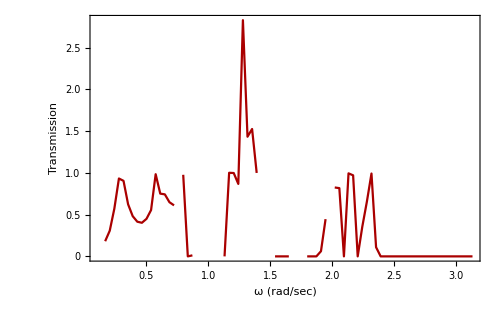

```mathematica
(****************************************** Parameters ********************************)
mChannel =1(*.12*); mSource=1(*.047*); mDrain=mSource;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;

kVerticalChannel = 1;kHorizontalChannel = 1(*13.7*);
kVerticalSource=1;kHorizontalSource= 1(*15.3*);
kVerticalDrain=kVerticalSource; kHorizontalDrain=kHorizontalSource;
kSC =1(*15.3*)(*(kHorizontalChannel+kHorizontalSource)/2*); kCD = kSC (*(kHorizontalChannel+kHorizontalDrain)/2*);
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,12}];

(****************************************** dynamical Matrix ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]]
KChannel = Table[If[r==c,If[(MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]]) || (MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]]),kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@latticeCoordinates},{c, 1, Length@latticeCoordinates}];

(**********************************Couplings******************************************)
cSource = Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
cDrain = cSource;

(**********************************Leads******************************************)
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
αDrain= Table[If[r==c,If[latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]},{c, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]}];

βSource=Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}];
βDrain=βSource;

Map[MatrixForm,{KChannel,cSource,αSource,βSource}];

(************************************ Transmission Calculation ********************************************)
transmission=ParallelTable[
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSource ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}],AccuracyGoal->4,PrecisionGoal->4,MaxIterations->10000];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mDrain ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.βDrain.GS11.ConjugateTranspose[βDrain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}],AccuracyGoal->4,PrecisionGoal->4,MaxIterations->10000];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(Length@surfaceElements1-1),cDrain.Partition[Values[sol],{Length@cDrain}].ConjugateTranspose[cDrain],0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[((mChannel*IdentityMatrix[Length@KChannel] ω1^2 +ⅈ η)- KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.17,3.13,.037}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission//Chop,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

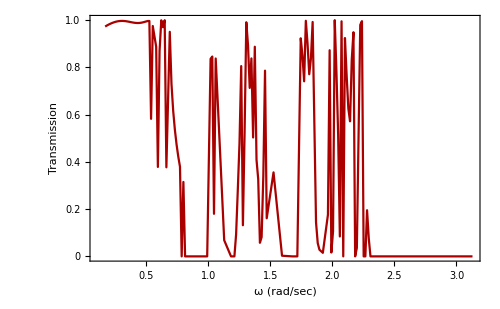

```mathematica
transmission =Select[transmission,Im[#[[2]]]==0&];
tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

```mathematica
transmission
```

{{0.17,0.993825},{0.207,0.995235},{0.244,0.996255},{0.281,0.997033},{0.318,0.997647},{0.355,0.998142},{0.392,48.1826+0.0000594829 ⅈ},{0.429,0.99888},{0.466,0.999154},{0.503,0.999378},{0.54,0.999559},{0.577,0.999702},{0.614,0.999813},{0.651,0.999896},{0.688,0.999953},{0.725,0.999987},{0.762,1.},{0.799,1.99999},{0.836,71.2872+0.000954545 ⅈ},{0.873,-2.63159×10^7+95349. ⅈ},{0.91,1.97583×10^-10},{0.947,2.},{0.984,0},{1.021,1.06043×10^-10},{1.058,-3.2958×10^9-60478.1 ⅈ},{1.095,3.20614×10^-9},{1.132,1.99993},{1.169,1.9999},{1.206,1.99991},{1.243,1.99991},{1.28,1.99989},{1.317,1.99991},{1.354,1.99993},{1.391,1.99996},{1.428,7.89118×10^-9},{1.465,3.74506×10^-8},{1.502,3.39419×10^-8},{1.539,3.42662×10^-8},{1.576,4.34646×10^-10},{1.613,0.999998},{1.65,0.999995},{1.687,0.999993},{1.724,0.999994},{1.761,0.999995},{1.798,0.999998},{1.835,1.},{1.872,2.},{1.909,37.3584+0.0018902 ⅈ},{1.946,2.},{1.983,2.88993×10^-10},{2.02,0.999995},{2.057,0.999994},{2.094,0.999995},{2.131,0.999998},{2.168,1.},{2.205,0.999999},{2.242,0.999992},{2.279,0.999982},{2.316,0.99998},{2.353,0},{2.39,0},{2.427,0},{2.464,0},{2.501,0},{2.538,0},{2.575,0},{2.612,0},{2.649,0},{2.686,0},{2.723,0},{2.76,0},{2.797,0},{2.834,0},{2.871,0},{2.908,0},{2.945,0},{2.982,0},{3.019,0},{3.056,0},{3.093,0},{3.13,0}}

#### Transmission (inspect)

```mathematica
(****************************************** Parameters ********************************)
mChannel =1(*.12*); mSource=1(*.047*); mDrain=mSource;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;

kVerticalChannel = 1;kHorizontalChannel = 1(*13.7*);
kVerticalSource=1;kHorizontalSource= 1(*15.3*);
kVerticalDrain=kVerticalSource; kHorizontalDrain=kHorizontalSource;
kSC =1(*15.3*)(*(kHorizontalChannel+kHorizontalSource)/2*); kCD = kSC (*(kHorizontalChannel+kHorizontalDrain)/2*);
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,8}];

(****************************************** dynamical Matrix ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]]
KChannel = Table[If[r==c,If[(MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]]) || (MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]]),kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@latticeCoordinates},{c, 1, Length@latticeCoordinates}];

(**********************************Couplings******************************************)
cSource = Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
cDrain = cSource;

(**********************************Leads******************************************)
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
αDrain= Table[If[r==c,If[latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]},{c, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]}];

βSource=Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}];
βDrain=βSource;

(*Map[MatrixForm,{KChannel(*,mChannel*IdentityMatrix[Length@KChannel]*),cSource,αSource,αDrain,βSource,βDrain}]*)

(************************************ Transmission Calculation ********************************************)
ω1=1.058;
(*transmission=ParallelTable[*)
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSC ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}],AccuracyGoal->4,PrecisionGoal->4,MaxIterations->1000];
ΣS = SetPrecision[ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]],3];
ΓS =Chop[-2Im[ΣS],0.0000001];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mCD ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.βDrain.GS11.ConjugateTranspose[βDrain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}],AccuracyGoal->4,PrecisionGoal->4,MaxIterations->1000];
ΣD=SetPrecision[ArrayFlatten[Table[If[i==j==Length@KChannel-(Length@surfaceElements1-1),cDrain.Partition[Values[sol],{Length@cDrain}].ConjugateTranspose[cDrain],0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]],3];
ΓD=Chop[-2Im[ΣD],0.0000001];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[((mChannel*IdentityMatrix[Length@KChannel] ω1^2 +ⅈ η)- KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
Chop[ Tr[ΓS.GR.ΓD.GA]]
(*{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.11,3,.0131}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]*)
Map[MatrixForm,{(*GR,*)ΣS,ΣD,ΓS,ΓD}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

-1.92943×10^9-7148.17 ⅈ

{(-0.344+0. ⅈ | 0.61+0.712 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.61-0.712 ⅈ | 0.344+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.344+0. ⅈ | 0.61+0.712 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.61-0.712 ⅈ | 0.344+0. ⅈ),(0. | -1.42 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.42 | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | -1.42
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.42 | 0.)}

```mathematica
a={{-4,1,3,0},{-2,7,1,-1},{1,-1,9,-3},{-1,0,5,-10}};
X=Array[x,{4,4}]
sol=NSolve[-2 a.X+X^2+IdentityMatrix[4]==Array[0&,{4,4}],Flatten[X]]
X/. Flatten[sol]//MatrixForm
```

{{x[1,1],x[1,2],x[1,3],x[1,4]},{x[2,1],x[2,2],x[2,3],x[2,4]},{x[3,1],x[3,2],x[3,3],x[3,4]},{x[4,1],x[4,2],x[4,3],x[4,4]}}

{{x[1,1]→-13.7806+0.987323 ⅈ,x[1,2]→-13.828+0.984457 ⅈ,x[1,3]→-13.8394+1.04071 ⅈ,x[1,4]→-13.8321+0.978826 ⅈ,x[2,1]→17.5179-0.372219 ⅈ,x[2,2]→17.4792-0.373458 ⅈ,x[2,3]→17.5292-0.393256 ⅈ,x[2,4]→17.5306-0.369357 ⅈ,x[3,1]→7.44159-3.0948 ⅈ,x[3,2]→7.44358-3.10058 ⅈ,x[3,3]→7.44528-3.28222 ⅈ,x[3,4]→7.44173-3.08485 ⅈ,x[4,1]→4.25868-1.15448 ⅈ,x[4,2]→4.26282-1.15597 ⅈ,x[4,3]→4.2698-1.22299 ⅈ,x[4,4]→4.22711-1.15294 ⅈ},{1},65532,{1},{x[1,1]→-0.122968,x[1,2]→0.0240829,12,x[4,3]→0.0252467,x[4,4]→-0.0577913}}
 |  |  |  |

(-13.7806+0.987323 ⅈ | -13.828+0.984457 ⅈ | -13.8394+1.04071 ⅈ | -13.8321+0.978826 ⅈ
17.5179-0.372219 ⅈ | 17.4792-0.373458 ⅈ | 17.5292-0.393256 ⅈ | 17.5306-0.369357 ⅈ
7.44159-3.0948 ⅈ | 7.44358-3.10058 ⅈ | 7.44528-3.28222 ⅈ | 7.44173-3.08485 ⅈ
4.25868-1.15448 ⅈ | 4.26282-1.15597 ⅈ | 4.2698-1.22299 ⅈ | 4.22711-1.15294 ⅈ)

```mathematica
ω1=.11;
gS11=Inverse[(mSC ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}];
sol=NSolve[(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11==Array[0&,{Length@gS11,Length@gS11}],Flatten[GS11],WorkingPrecision->5];
GS11/. Flatten[sol]//MatrixForm;
sols=ParallelTable[
mat=GS11/. Flatten[sol[[i]]];
SetPrecision[ConjugateTranspose[cSource].mat.cSource,5],{i,Length@sol}];
```

```mathematica
Transpose@sols[[2]]==sols[[2]]
```

True

```mathematica
ParallelTable[
mat=GS11/. Flatten[sol[[i]]];
sigma=SetPrecision[ConjugateTranspose[cSource].mat.cSource,5];
sigma==Transpose[sigma],{i,Length@sol}]
```

{False,True,True,False,True,True}

```mathematica
Print[Length@gS11," ", Length@αSource," ",Length@cSource," ", Length@mat, " " ,Length@sol]
```

8 8 8 8 6

#### Transmission (inspect) using different solve method

```mathematica
(****************************************** Parameters ********************************)
mChannel =1(*.12*); mSource=1(*.047*); mDrain=mSource;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;

kVerticalChannel = 1;kHorizontalChannel = 1(*13.7*);
kVerticalSource=1;kHorizontalSource= 1(*15.3*);
kVerticalDrain=kVerticalSource; kHorizontalDrain=kHorizontalSource;
kSC =1(*15.3*)(*(kHorizontalChannel+kHorizontalSource)/2*); kCD = kSC (*(kHorizontalChannel+kHorizontalDrain)/2*);
η=0.0001;
surfaceElements1=Sort@Table[i,{i,1,8}];

(****************************************** dynamical Matrix ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
KChannel = Table[If[r==c,If[(MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]]) || (MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]]),kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@latticeCoordinates},{c, 1, Length@latticeCoordinates}];

(**********************************Couplings******************************************)
cSource = Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
cDrain = cSource;

(**********************************Leads******************************************)
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
αDrain= Table[If[r==c,If[latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]},{c, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]}];

βSource=Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}];
βDrain=βSource;

(*Map[MatrixForm,{KChannel,mChannel*IdentityMatrix[Length@KChannel],cSource,αSource,αDrain,βSource}]*)

(************************************ Transmission Calculation ********************************************)
ω1=.873;
(*transmission=ParallelTable[*)
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSC ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}];
sol=SortBy[NSolve[(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11==Array[0&,{Length@gS11,Length@gS11}],Flatten[GS11],WorkingPrecision->5],First];
sols=SortBy[ParallelTable[
mat=GS11/. Flatten[sol[[i]]](*;
SetPrecision[ConjugateTranspose[cSource].mat.cSource,5]*),{i,Length@sol}],First];
Map[MatrixForm,sols]
(*ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].mat.cSource,0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓS =Chop[-2Im[ΣS],0.0000001];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mCD ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αDrain];
GS11=Array[x,{Length@αSource,Length@αSource}];
sol=NSolve[(gS11.βDrain.GS11.ConjugateTranspose[βDrain]-IdentityMatrix[Length@gS11]).GS11+gS11==Array[0&,{Length@gS11,Length@gS11}],Flatten[GS11],WorkingPrecision->5];
        mat=GS11/. Flatten[sol[[3]]];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(Length@surfaceElements1-1),cDrain.mat.ConjugateTranspose[cDrain],0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓD=Chop[-2Im[ΣD],0.0000001];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[((mChannel*IdentityMatrix[Length@KChannel] ω1^2 +ⅈ η)- KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];*)

(*{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.11,1,.131}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]*)

(*Chop[ Tr[ΓS.GR.ΓD.GA]]
Map[MatrixForm,{(*GR,*)ΣS,ΣD,ΓS,ΓD}]*)
```

{(-0.231392-0.00019293 ⅈ | -0.134744+0.000359481 ⅈ | 0.484131-0.000379458 ⅈ | 0.00934513+0.000089674 ⅈ | 0.830684-0.000325202 ⅈ | 0.38705+0.0000331939 ⅈ | 0.544148-0.00010617 ⅈ | 0.312674+0.0000520743 ⅈ
-0.134744+0.000359481 ⅈ | 1.89645-0.0021268 ⅈ | -1.24453+0.001382 ⅈ | 0.919725-0.000800589 ⅈ | -1.40582+0.00147571 ⅈ | 0.296516-0.000116268 ⅈ | -0.495697+0.000585321 ⅈ | 0.239537-0.0000745748 ⅈ
0.484131-0.000379458 ⅈ | -1.24453+0.001382 ⅈ | 1.03615-0.00136171 ⅈ | 0.0466999+0.000463596 ⅈ | 1.79848-0.00140978 ⅈ | 0.864906+0.0000302566 ⅈ | 1.19014-0.000563263 ⅈ | 0.698705+0.0000808865 ⅈ
0.00934513+0.000089674 ⅈ | 0.919725-0.000800589 ⅈ | 0.0466999+0.000463596 ⅈ | -0.0400598-0.000409186 ⅈ | 0.0484633+0.000479528 ⅈ | -0.0187186-0.000200784 ⅈ | 0.0132915+0.000125152 ⅈ | -0.0151216-0.000163423 ⅈ
0.830684-0.000325202 ⅈ | -1.40582+0.00147571 ⅈ | 1.79848-0.00140978 ⅈ | 0.0484633+0.000479528 ⅈ | 1.39561-0.00159977 ⅈ | 0.683593-0.0000822308 ⅈ | 0.929096-0.000710092 ⅈ | 0.552233-0.0000218177 ⅈ
0.38705+0.0000331939 ⅈ | 0.296516-0.000116268 ⅈ | 0.864906+0.0000302566 ⅈ | -0.0187186-0.000200784 ⅈ | 0.683593-0.0000822308 ⅈ | -0.725456-0.000364383 ⅈ | -0.0187066-0.000200407 ⅈ | -0.586051-0.000341707 ⅈ
0.544148-0.00010617 ⅈ | -0.495697+0.000585321 ⅈ | 1.19014-0.000563263 ⅈ | 0.0132915+0.000125152 ⅈ | 0.929096-0.000710092 ⅈ | -0.0187066-0.000200407 ⅈ | -0.0400426-0.000408649 ⅈ | -0.0151119-0.000163117 ⅈ
0.312674+0.0000520743 ⅈ | 0.239537-0.0000745748 ⅈ | 0.698705+0.0000808865 ⅈ | -0.0151216-0.000163423 ⅈ | 0.552233-0.0000218177 ⅈ | -0.586051-0.000341707 ⅈ | -0.0151119-0.000163117 ⅈ | -1.28127-0.00037955 ⅈ),(-0.0507357-0.00059616 ⅈ | -3.40049-0.00153606 ⅈ | 2.71162+0.00109791 ⅈ | -1.55852-0.00119626 ⅈ | 3.40737+0.00168407 ⅈ | -0.0365411-0.000389003 ⅈ | 1.50627+0.000646011 ⅈ | -0.0295193-0.000316636 ⅈ
-3.40049-0.00153606 ⅈ | -117.269+1.29111 ⅈ | 96.2228-1.03495 ⅈ | -53.2353+0.574296 ⅈ | 122.512-1.28922 ⅈ | 1.5353+0.000951823 ⅈ | 55.4309-0.573189 ⅈ | 1.24028+0.000869113 ⅈ
2.71162+0.00109791 ⅈ | 96.2228-1.03495 ⅈ | -77.9557+0.829099 ⅈ | 44.4786-0.460187 ⅈ | -98.2106+1.03302 ⅈ | 0.603035-0.000437617 ⅈ | -43.6163+0.459462 ⅈ | 0.487155-0.000314169 ⅈ
-1.55852-0.00119626 ⅈ | -53.2353+0.574296 ⅈ | 44.4786-0.460187 ⅈ | -24.6251+0.255195 ⅈ | 56.6173-0.572904 ⅈ | 0.686074+0.000456607 ⅈ | 25.6062-0.254656 ⅈ | 0.554237+0.000413638 ⅈ
3.40737+0.00168407 ⅈ | 122.512-1.28922 ⅈ | -98.2106+1.03302 ⅈ | 56.6173-0.572904 ⅈ | -124.979+1.28688 ⅈ | 0.783021-0.000213014 ⅈ | -55.4975+0.57247 ⅈ | 0.632555-0.000120981 ⅈ
-0.0365411-0.000389003 ⅈ | 1.5353+0.000951823 ⅈ | 0.603035-0.000437617 ⅈ | 0.686074+0.000456607 ⅈ | 0.783021-0.000213014 ⅈ | 0.0365851+0.000390399 ⅈ | 0.366244+0.000095631 ⅈ | 0.0295548+0.000317767 ⅈ
1.50627+0.000646011 ⅈ | 55.4309-0.573189 ⅈ | -43.6163+0.459462 ⅈ | 25.6062-0.254656 ⅈ | -55.4975+0.57247 ⅈ | 0.366244+0.000095631 ⅈ | -25.0825+0.254732 ⅈ | 0.295866+0.000101156 ⅈ
-0.0295193-0.000316636 ⅈ | 1.24028+0.000869113 ⅈ | 0.487155-0.000314169 ⅈ | 0.554237+0.000413638 ⅈ | 0.632555-0.000120981 ⅈ | 0.0295548+0.000317767 ⅈ | 0.295866+0.000101156 ⅈ | -0.783963+0.000193373 ⅈ),(-0.00779758+0.0342706 ⅈ | -0.960563+0.784233 ⅈ | 0.754957-0.662717 ⅈ | -0.442438+0.35225 ⅈ | 0.942271-0.854704 ⅈ | -0.0217238-0.0301705 ⅈ | 0.411367-0.395391 ⅈ | -0.0175473-0.0243743 ⅈ
-0.960563+0.784233 ⅈ | 1.31964-5.7035 ⅈ | 0.557799+3.1193 ⅈ | 0.909378-2.88372 ⅈ | 1.65136+3.077 ⅈ | 1.6757-1.53421 ⅈ | 1.48668+0.689468 ⅈ | 1.3538-1.23929 ⅈ
0.754957-0.662717 ⅈ | 0.557799+3.1193 ⅈ | -0.801466-1.32262 ⅈ | 0.79686+1.64967 ⅈ | -0.747201-0.974437 ⅈ | 0.470679+1.23509 ⅈ | -0.12357+0.116468 ⅈ | 0.380152+0.997784 ⅈ
-0.442438+0.35225 ⅈ | 0.909378-2.88372 ⅈ | 0.79686+1.64967 ⅈ | 0.095568-1.44443 ⅈ | 1.42901+1.68975 ⅈ | 0.746785-0.700979 ⅈ | 0.972243+0.441881 ⅈ | 0.603327-0.566229 ⅈ
0.942271-0.854704 ⅈ | 1.65136+3.077 ⅈ | -0.747201-0.974437 ⅈ | 1.42901+1.68975 ⅈ | -1.86731-0.351448 ⅈ | 0.604487+1.55901 ⅈ | -0.56432+0.539576 ⅈ | 0.488226+1.25946 ⅈ
-0.0217238-0.0301705 ⅈ | 1.6757-1.53421 ⅈ | 0.470679+1.23509 ⅈ | 0.746785-0.700979 ⅈ | 0.604487+1.55901 ⅈ | 0.01716-0.0043904 ⅈ | 0.277754+0.694698 ⅈ | 0.0138628-0.00354561 ⅈ
0.411367-0.395391 ⅈ | 1.48668+0.689468 ⅈ | -0.12357+0.116468 ⅈ | 0.972243+0.441881 ⅈ | -0.56432+0.539576 ⅈ | 0.277754+0.694698 ⅈ | -0.574931+0.551513 ⅈ | 0.224335+0.561222 ⅈ
-0.0175473-0.0243743 ⅈ | 1.3538-1.23929 ⅈ | 0.380152+0.997784 ⅈ | 0.603327-0.566229 ⅈ | 0.488226+1.25946 ⅈ | 0.0138628-0.00354561 ⅈ | 0.224335+0.561222 ⅈ | -0.796639-0.00292864 ⅈ),(-0.00704887-0.034458 ⅈ | -0.962251-0.785465 ⅈ | 0.7556+0.663395 ⅈ | -0.443121-0.353134 ⅈ | 0.942451+0.85558 ⅈ | -0.0223825+0.0296992 ⅈ | 0.411118+0.395608 ⅈ | -0.0180834+0.0239907 ⅈ
-0.962251-0.785465 ⅈ | 1.32413+5.7076 ⅈ | 0.556373-3.12284 ⅈ | 0.910563+2.88558 ⅈ | 1.65066-3.08026 ⅈ | 1.67614+1.53533 ⅈ | 1.48662-0.690292 ⅈ | 1.35395+1.2404 ⅈ
0.7556+0.663395 ⅈ | 0.556373-3.12284 ⅈ | -0.801785+1.32434 ⅈ | 0.79655-1.65116 ⅈ | -0.747974+0.976043 ⅈ | 0.470438-1.23573 ⅈ | -0.124013-0.116047 ⅈ | 0.380119-0.998238 ⅈ
-0.443121-0.353134 ⅈ | 0.910563+2.88558 ⅈ | 0.79655-1.65116 ⅈ | 0.095571+1.4451 ⅈ | 1.42898-1.69087 ⅈ | 0.746578+0.701498 ⅈ | 0.972176-0.442062 ⅈ | 0.603069+0.566745 ⅈ
0.942451+0.85558 ⅈ | 1.65066-3.08026 ⅈ | -0.747974+0.976043 ⅈ | 1.42898-1.69087 ⅈ | -1.86825+0.35271 ⅈ | 0.6046-1.55942 ⅈ | -0.564641-0.539247 ⅈ | 0.488521-1.25972 ⅈ
-0.0223825+0.0296992 ⅈ | 1.67614+1.53533 ⅈ | 0.470438-1.23573 ⅈ | 0.746578+0.701498 ⅈ | 0.6046-1.55942 ⅈ | 0.0170631+0.00476168 ⅈ | 0.277823-0.694691 ⅈ | 0.0137839+0.00384778 ⅈ
0.411118+0.395608 ⅈ | 1.48662-0.690292 ⅈ | -0.124013-0.116047 ⅈ | 0.972176-0.442062 ⅈ | -0.564641-0.539247 ⅈ | 0.277823-0.694691 ⅈ | -0.574994-0.551415 ⅈ | 0.224482-0.56118 ⅈ
-0.0180834+0.0239907 ⅈ | 1.35395+1.2404 ⅈ | 0.380119-0.998238 ⅈ | 0.603069+0.566745 ⅈ | 0.488521-1.25972 ⅈ | 0.0137839+0.00384778 ⅈ | 0.224482-0.56118 ⅈ | -0.796704+0.00304402 ⅈ),(0.00757256+0.0000946647 ⅈ | -0.870016-0.950043 ⅈ | 0.66029+0.73391 ⅈ | -0.404938-0.440011 ⅈ | 0.809855+0.908325 ⅈ | -0.0438003-0.0346981 ⅈ | 0.342297+0.390398 ⅈ | -0.0353813-0.0280333 ⅈ
-0.871863+0.950671 ⅈ | 7.94405-0.00177496 ⅈ | -4.70991-1.55892 ⅈ | 3.94747-0.294412 ⅈ | -4.95855-2.87994 ⅈ | 1.76172-1.60815 ⅈ | -1.42843-2.00558 ⅈ | 1.42329-1.29901 ⅈ
0.661168-0.735186 ⅈ | -4.70983+1.56238 ⅈ | 3.42456-0.00192091 ⅈ | -1.61237+0.950318 ⅈ | 4.578+0.732465 ⅈ | 0.440479+1.29966 ⅈ | 2.24248+0.908161 ⅈ | 0.355751+1.04994 ⅈ
-0.406154+0.439919 ⅈ | 3.94781+0.294755 ⅈ | -1.61225-0.950055 ⅈ | 1.49031+0.000458796 ⅈ | -1.58969-1.6158 ⅈ | 0.793464-0.733796 ⅈ | -0.355751-1.04994 ⅈ | 0.641039-0.592737 ⅈ
0.810794-0.910226 ⅈ | -4.95998+2.88454 ⅈ | 4.57888-0.73663 ⅈ | -1.59087+1.61654 ⅈ | 4.85719-0.00208539 ⅈ | 0.589186+1.64346 ⅈ | 2.4337+0.733563 ⅈ | 0.47586+1.32769 ⅈ
-0.0445865+0.0337573 ⅈ | 1.76069+1.61105 ⅈ | 0.441522-1.30093 ⅈ | 0.792587+0.7353 ⅈ | 0.591003-1.64419 ⅈ | 0.0576814+0.000623277 ⅈ | 0.2899-0.734418 ⅈ | 0.0465972+0.000507272 ⅈ
0.3424-0.391638 ⅈ | -1.42971+2.0088 ⅈ | 2.24342-0.91039 ⅈ | -0.356763+1.05091 ⅈ | 2.43458-0.735533 ⅈ | 0.289022+0.734678 ⅈ | 0.770196-0.000347574 ⅈ | 0.233435+0.59352 ⅈ
-0.0360209+0.0272675 ⅈ | 1.42224+1.30158 ⅈ | 0.356763-1.05091 ⅈ | 0.640234+0.594055 ⅈ | 0.477542-1.3282 ⅈ | 0.0465972+0.000507272 ⅈ | 0.23424-0.593272 ⅈ | -0.770196+0.000347574 ⅈ),(0.00757256+0.0000946647 ⅈ | -0.871863+0.950671 ⅈ | 0.661168-0.735186 ⅈ | -0.406154+0.439919 ⅈ | 0.810794-0.910226 ⅈ | -0.0445865+0.0337573 ⅈ | 0.3424-0.391638 ⅈ | -0.0360209+0.0272675 ⅈ
-0.870016-0.950043 ⅈ | 7.94405-0.00177496 ⅈ | -4.70983+1.56238 ⅈ | 3.94781+0.294755 ⅈ | -4.95998+2.88454 ⅈ | 1.76069+1.61105 ⅈ | -1.42971+2.0088 ⅈ | 1.42224+1.30158 ⅈ
0.66029+0.73391 ⅈ | -4.70991-1.55892 ⅈ | 3.42456-0.00192091 ⅈ | -1.61225-0.950055 ⅈ | 4.57888-0.73663 ⅈ | 0.441522-1.30093 ⅈ | 2.24342-0.91039 ⅈ | 0.356763-1.05091 ⅈ
-0.404938-0.440011 ⅈ | 3.94747-0.294412 ⅈ | -1.61237+0.950318 ⅈ | 1.49031+0.000458796 ⅈ | -1.59087+1.61654 ⅈ | 0.792587+0.7353 ⅈ | -0.356763+1.05091 ⅈ | 0.640234+0.594055 ⅈ
0.809855+0.908325 ⅈ | -4.95855-2.87994 ⅈ | 4.578+0.732465 ⅈ | -1.58969-1.6158 ⅈ | 4.85719-0.00208539 ⅈ | 0.591003-1.64419 ⅈ | 2.43458-0.735533 ⅈ | 0.477542-1.3282 ⅈ
-0.0438003-0.0346981 ⅈ | 1.76172-1.60815 ⅈ | 0.440479+1.29966 ⅈ | 0.793464-0.733796 ⅈ | 0.589186+1.64346 ⅈ | 0.0576814+0.000623277 ⅈ | 0.289022+0.734678 ⅈ | 0.0465972+0.000507272 ⅈ
0.342297+0.390398 ⅈ | -1.42843-2.00558 ⅈ | 2.24248+0.908161 ⅈ | -0.355751-1.04994 ⅈ | 2.4337+0.733563 ⅈ | 0.2899-0.734418 ⅈ | 0.770196-0.000347574 ⅈ | 0.23424-0.593272 ⅈ
-0.0353813-0.0280333 ⅈ | 1.42329-1.29901 ⅈ | 0.355751+1.04994 ⅈ | 0.641039-0.592737 ⅈ | 0.47586+1.32769 ⅈ | 0.0465972+0.000507272 ⅈ | 0.233435+0.59352 ⅈ | -0.770196+0.000347574 ⅈ)}

```mathematica
transmission//Chop
```

{{0.11,0.000189786+0.000104924 ⅈ},{0.241,0.0000181301+0.0000999327 ⅈ},{0.372,-0.000159652+0.0000857906 ⅈ},{0.503,0.000127894-0.0000598313 ⅈ},{0.634,0.0000247413-5.58547×10^-7 ⅈ},{0.765,-7.4411},{0.896,0.000100443-10.3646 ⅈ}}

```mathematica
symmetricSolutions=Map[MatrixForm,Select[sols,SymmetricMatrixQ]]
```

{}

```mathematica
stableSolutions=Map[MatrixForm,Select[sols,AllTrue[Eigenvalues[#],Re[#]<=0&]&]]
```

{}

### Armchair - 3

#### Model

```mathematica
(********************************************* Function to generate spring between two points *********************************************)
generateSpring[p1_,p2_,turns_,springRadius_,tubeRadius_]:=Module[{vector,length,direction,helixPath,alignmentMatrix},
vector=p2-p1;
length=Norm[vector];
(*Handle the degenerate case where the points coincide*)
If[length==0,Return[Graphics3D[]]];
direction=vector/length;(*Normalize the direction vector*)
helixPath=Table[{springRadius Cos[2 Pi turns z/length],springRadius Sin[2 Pi turns z/length],z},{z,0,length,0.01}];(* helical path along the z-axis*)
alignmentMatrix=RotationMatrix3D[VectorAngle[{0,0,1},direction],Cross[{0,0,1},direction]];
helixPath=Map[alignmentMatrix.#+p1&,helixPath];(*Apply the alignment and translate the helix to p1*)
Graphics3D[{Black,Tube[helixPath,tubeRadius]}]];

(*Rotation matrix in 3D for a given axis and angle*)
RotationMatrix3D[angle_,axis_]:=Module[{c=Cos[angle],s=Sin[angle],v=1-Cos[angle],x,y,z},{x,y,z}=Normalize[axis];
{{x x v+c,x y v-z s,x z v+y s},{x y v+z s,y y v+c,y z v-x s},{x z v-y s,y z v+x s,z z v+c}}];

(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}};
ax = {3,0};
ay = {0,√3};
nx=3; ny=4;
latticeCoordinates= supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
maxY=Max[latticeCoordinates[[All,2]]];
latticeCoordinates= supercellCoordinates=Select[latticeCoordinates,#[[2]]<maxY&];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

masses=Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[latticeCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@latticeCoordinates}],ViewPoint->Above,ImageSize->700];
springs=Show[Table[generateSpring[Append[hoppings[[i,1]],0],Append[hoppings[[i,2]],0],5,0.1,0.015],{i,1,Length@hoppings}]];
label = Show[Table[Graphics3D[Text[Style[i,20,White],Append[latticeCoordinates[[i]],0]]],{i,1,Length[latticeCoordinates]}]];
Show[masses,springs,label]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{4,5}},{2,{5,6}},{3,{6,7}},{4,{1,8}},{5,{1,2,9}},{6,{2,3,10}},{7,{3,11}},{8,{4,12}},{9,{5,12,13}},{10,{6,13,14}},{11,{7,14}},{12,{8,9,15}},{13,{9,10,16}},{14,{10,11,17}},{15,{12,18,19}},{16,{13,19,20}},{17,{14,20,21}},{18,{15,22}},{19,{15,16,23}},{20,{16,17,24}},{21,{17,25}},{22,{18,26}},{23,{19,26,27}},{24,{20,27,28}},{25,{21,28}},{26,{22,23,29}},{27,{23,24,30}},{28,{24,25,31}},{29,{26,32,33}},{30,{27,33,34}},{31,{28,34,35}},{32,{29,36}},{33,{29,30,37}},{34,{30,31,38}},{35,{31,39}},{36,{32,40}},{37,{33,40,41}},{38,{34,41,42}},{39,{35,42}},{40,{36,37}},{41,{37,38}},{42,{38,39}}}

#### Transmission

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,29,30,31,32,33,34,35,36,37,38,39,40,41,42}

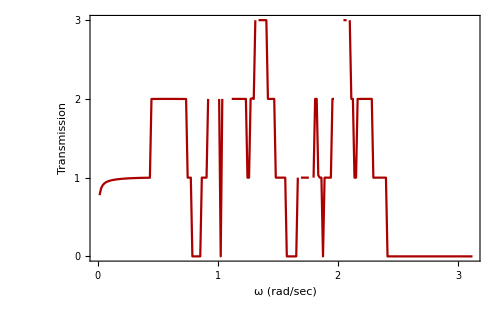

```mathematica
(****************************************** Parameters ********************************)
mChannel =1(*.12*); mSource=1(*.047*); mDrain=mSource;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;

kVerticalChannel = 1;kHorizontalChannel = 1(*13.7*);
kVerticalSource=1;kHorizontalSource= 1(*15.3*);
kVerticalDrain=kVerticalSource; kHorizontalDrain=kHorizontalSource;
kSC =1 (*15.3*)(*(kHorizontalChannel+kHorizontalSource)/2*); kCD = kSC (*(kHorizontalChannel+kHorizontalDrain)/2*);
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,14}];

(****************************************** dynamical Matrix ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]]
KChannel = Table[If[r==c,If[(MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]]) || (MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]]),kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@latticeCoordinates},{c, 1, Length@latticeCoordinates}];

(**********************************Couplings******************************************)
cSource = Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
cDrain = cSource;

(**********************************Leads******************************************)
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalSource],If[MemberQ[NNHI[[r,2]],c],-kHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
αDrain= Table[If[r==c,If[latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalDrain,Length@NNHI[[r,2]]*kHorizontalDrain],If[MemberQ[NNHI[[r,2]],c],-kHorizontalDrain,0]],{r, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]},{c, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]}];

βSource=Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}];
βDrain=βSource;

Map[MatrixForm,{KChannel,cSource,αSource,βSource}];

(************************************ Transmission Calculation ********************************************)
transmission=ParallelTable[
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSource ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}],PrecisionGoal->4,MaxIterations->10000];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mDrain ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.βDrain.GS11.ConjugateTranspose[βDrain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}],PrecisionGoal->4,MaxIterations->10000];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(Length@surfaceElements1-1),cDrain.Partition[Values[sol],{Length@cDrain}].ConjugateTranspose[cDrain],0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[((mChannel*IdentityMatrix[Length@KChannel] ω1^2 +ⅈ η)- KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.017,3.13,.0131}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

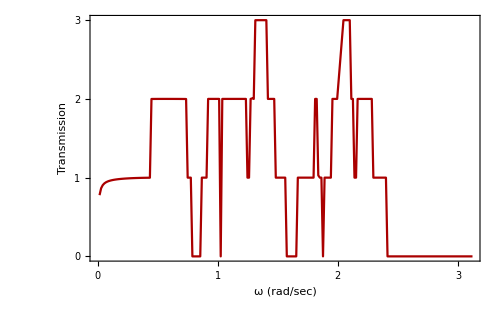

```mathematica
transmission =Select[transmission,Im[#[[2]]]==0&];
tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

```mathematica
transmission
```

{{0.017,0},{0.0301,0},{0.0432,0},{0.0563,0},{0.0694,0},{0.0825,0},{0.0956,0},{0.1087,0},{0.1218,0},{0.1349,0},{0.148,0},{0.1611,0},{0.1742,0},{0.1873,0},{0.2004,0},{0.2135,0},{0.2266,0},{0.2397,0},{0.2528,0},{0.2659,0},{0.279,0},{0.2921,0},{0.3052,0},{0.3183,0},{0.3314,0},{0.3445,0},{0.3576,0},{0.3707,0},{0.3838,0},{0.3969,0},{0.41,0},{0.4231,0},{0.4362,0},{0.4493,0},{0.4624,0},{0.4755,0},{0.4886,0},{0.5017,0},{0.5148,0},{0.5279,0},{0.541,0},{0.5541,0},{0.5672,0},{0.5803,0},{0.5934,0},{0.6065,0},{0.6196,0},{0.6327,0},{0.6458,0},{0.6589,0},{0.672,0},{0.6851,0},{0.6982,0},{0.7113,0},{0.7244,0},{0.7375,0},{0.7506,0},{0.7637,0},{0.7768,0},{0.7899,0},{0.803,0},{0.8161,0},{0.8292,0},{0.8423,0},{0.8554,0},{0.8685,0},{0.8816,0},{0.8947,0},{0.9078,0},{0.9209,0},{0.934,0},{0.9471,0},{0.9602,0},{0.9733,0},{0.9864,0},{0.9995,0},{1.0126,0},{1.0257,0},{1.0388,0},{1.0519,0},{1.065,0},{1.0781,0},{1.0912,0},{1.1043,0},{1.1174,0},{1.1305,0},{1.1436,1.18454×10^-10},{1.1567,7.84825×10^-10},{1.1698,3.02891×10^-9},{1.1829,2.06084×10^-10},{1.196,0},{1.2091,0},{1.2222,0},{1.2353,0},{1.2484,0},{1.2615,0},{1.2746,0},{1.2877,0},{1.3008,0},{1.3139,0},{1.327,0},{1.3401,0},{1.3532,0},{1.3663,0},{1.3794,0},{1.3925,0},{1.4056,0},{1.4187,0},{1.4318,0},{1.4449,0},{1.458,0},{1.4711,0},{1.4842,0},{1.4973,0},{1.5104,0},{1.5235,0},{1.5366,0},{1.5497,0},{1.5628,0},{1.5759,0},{1.589,0},{1.6021,0.0296618},{1.6152,0.13468},{1.6283,0.227358},{1.6414,0.30935},{1.6545,0.382056},{1.6676,0.446665},{1.6807,0.504188},{1.6938,0.555493},{1.7069,0.601327},{1.72,0.642333},{1.7331,0.679069},{1.7462,0.712018},{1.7593,0.741603},{1.7724,0.768193},{1.7855,0.792111},{1.7986,0.813641},{1.8117,0.833034},{1.8248,0.85051},{1.8379,0.866266},{1.851,0.880474},{1.8641,0.89329},{1.8772,0.90485},{1.8903,0.915278},{1.9034,0.924682},{1.9165,0.93316},{1.9296,0.940802},{1.9427,0.947685},{1.9558,0.953881},{1.9689,0.959454},{1.982,0.964461},{1.9951,0.968954},{2.0082,0.972981},{2.0213,0.976584},{2.0344,0.979802},{2.0475,0.982669},{2.0606,0.985218},{2.0737,0.987478},{2.0868,0.989473},{2.0999,0.99123},{2.113,0.992768},{2.1261,0.994108},{2.1392,0.995268},{2.1523,0.996265},{2.1654,0.997113},{2.1785,0.997826},{2.1916,0.998417},{2.2047,0.998897},{2.2178,0.999277},{2.2309,0.999565},{2.244,0.999772},{2.2571,0.999905},{2.2702,0.999971},{2.2833,0.999977},{2.2964,0.999929},{2.3095,0.999833},{2.3226,0.999693},{2.3357,0.999515},{2.3488,0.999303},{2.3619,0.99906},{2.375,0.998791},{2.3881,0.998498},{2.4012,0.998185},{2.4143,0.997854},{2.4274,0.997507},{2.4405,0.997148},{2.4536,0.996778},{2.4667,0.996398},{2.4798,0.996011},{2.4929,0.995618},{2.506,0.995221},{2.5191,0.99482},{2.5322,0.994417},{2.5453,0.994013},{2.5584,0.993609},{2.5715,0.993206},{2.5846,0.992804},{2.5977,0.992404},{2.6108,0.992007},{2.6239,0.991613},{2.637,0.991223},{2.6501,0.990837},{2.6632,0.990455},{2.6763,0.990078},{2.6894,0.989706},{2.7025,0.98934},{2.7156,0.988979},{2.7287,0.988624},{2.7418,0.988275},{2.7549,0.987932},{2.768,0.987595},{2.7811,0.987264},{2.7942,0.98694},{2.8073,1.18193},{2.8204,1.36661},{2.8335,1.49043},{2.8466,1.57876},{2.8597,1.64464},{2.8728,1.69543},{2.8859,1.73562},{2.899,1.76809},{2.9121,1.79478},{2.9252,1.81704},{2.9383,1.83583},{2.9514,1.85186},{2.9645,1.86566},{2.9776,1.87764},{2.9907,1.88811},{3.0038,1.89733},{3.0169,1.90548},{3.03,1.91274},{3.0431,1.91923},{3.0562,1.92505},{3.0693,1.9303},{3.0824,1.93504},{3.0955,1.93934},{3.1086,1.94325},{3.1217,1.94681},{3.1348,1.95007},{3.1479,1.95304},{3.161,1.95577},{3.1741,1.95826},{3.1872,1.96055},{3.2003,1.96266},{3.2134,1.96458},{3.2265,1.96635},{3.2396,1.96797},{3.2527,1.96945},{3.2658,1.97081},{3.2789,1.97204},{3.292,1.97316},{3.3051,1.97418},{3.3182,1.97509},{3.3313,1.97592},{3.3444,1.97665},{3.3575,1.9773},{3.3706,1.97786},{3.3837,1.97836},{3.3968,1.97878},{3.4099,1.97913},{3.423,1.97941},{3.4361,1.97963},{3.4492,1.97979},{3.4623,1.9799},{3.4754,1.97995},{3.4885,1.97995},{3.5016,1.9799},{3.5147,1.97981},{3.5278,1.97967},{3.5409,1.97949},{3.554,1.97928},{3.5671,1.97902},{3.5802,1.97874},{3.5933,1.97842},{3.6064,1.97807},{3.6195,1.97769},{3.6326,1.97729},{3.6457,1.97687},{3.6588,1.97643},{3.6719,1.97597},{3.685,1.97549},{3.6981,1.975},{3.7112,1.9745},{3.7243,1.97399},{3.7374,1.97347},{3.7505,1.97295},{3.7636,1.97242},{3.7767,1.97189},{3.7898,1.97136},{3.8029,1.97083},{3.816,1.9703},{3.8291,1.96978},{3.8422,1.96927},{3.8553,1.96877},{3.8684,1.96827},{3.8815,1.96779},{3.8946,1.96732},{3.9077,1.96687},{3.9208,1.96643},{3.9339,1.96601},{3.947,1.96561},{3.9601,1.96522},{3.9732,1.96486},{3.9863,1.96452},{3.9994,1.9642},{4.0125,1.9639},{4.0256,1.96363},{4.0387,1.96338},{4.0518,1.96316},{4.0649,1.96297},{4.078,1.9628},{4.0911,1.96266},{4.1042,1.96254},{4.1173,1.96245},{4.1304,1.9624},{4.1435,1.96236},{4.1566,1.96236},{4.1697,1.96239},{4.1828,1.96244},{4.1959,1.96252},{4.209,1.96263},{4.2221,1.96277},{4.2352,1.96294},{4.2483,1.96313},{4.2614,1.96335},{4.2745,1.96359},{4.2876,1.96386},{4.3007,1.96416},{4.3138,1.96448},{4.3269,1.96482},{4.34,1.96519},{4.3531,1.96557},{4.3662,1.96598},{4.3793,1.96641},{4.3924,1.96686},{4.4055,1.96732},{4.4186,1.96781},{4.4317,1.9683},{4.4448,1.96882},{4.4579,1.96934},{4.471,1.96988},{4.4841,1.97043},{4.4972,1.97099},{4.5103,1.97155},{4.5234,1.97213},{4.5365,1.97271},{4.5496,1.97329},{4.5627,1.97387},{4.5758,1.97446},{4.5889,1.97504},{4.602,1.97636},{4.6151,1.97794},{4.6282,1.97958},{4.6413,1.98127},{4.6544,1.98301},{4.6675,1.98482},{4.6806,1.98668},{4.6937,1.98861},{4.7068,1.99061},{4.7199,1.99269},{4.733,1.99486},{4.7461,1.99711},{4.7592,1.99946},{4.7723,2.00191},{4.7854,2.00447},{4.7985,2.00716},{4.8116,2.00998},{4.8247,2.01295},{4.8378,2.01608},{4.8509,2.01938},{4.864,2.02287},{4.8771,2.02656},{4.8902,2.03048},{4.9033,2.03464},{4.9164,2.03908},{4.9295,2.0438},{4.9426,2.04885},{4.9557,2.05425},{4.9688,2.06003},{4.9819,2.06623},{4.995,2.07288},{5.0081,2.08004},{5.0212,2.08773},{5.0343,2.09602},{5.0474,2.10496},{5.0605,2.1146},{5.0736,2.125},{5.0867,2.13622},{5.0998,2.14834},{5.1129,2.16143},{5.126,2.17554},{5.1391,2.19078},{5.1522,2.20719},{5.1653,2.22487},{5.1784,2.24388},{5.1915,2.26429},{5.2046,2.28616},{5.2177,2.30954},{5.2308,2.33445},{5.2439,2.36091},{5.257,2.38891},{5.2701,2.4184},{5.2832,2.44929},{5.2963,2.48147},{5.3094,2.51477},{5.3225,2.54896},{5.3356,2.58379},{5.3487,2.61894},{5.3618,2.65405},{5.3749,2.68872},{5.388,2.72253},{5.4011,2.75505},{5.4142,2.78585},{5.4273,2.81453},{5.4404,2.84072},{5.4535,2.86412},{5.4666,2.88448},{5.4797,2.90166},{5.4928,2.91556},{5.5059,2.9262},{5.519,2.93365},{5.5321,2.93805},{5.5452,2.9396},{5.5583,2.93853},{5.5714,2.93512},{5.5845,2.92965},{5.5976,2.92239},{5.6107,2.91365},{5.6238,2.90368},{5.6369,2.89274},{5.65,2.88107},{5.6631,2.86888},{5.6762,2.85635},{5.6893,2.84366},{5.7024,2.83094},{5.7155,2.81833},{5.7286,2.80592},{5.7417,2.79381},{5.7548,2.78206},{5.7679,2.77074},{5.781,2.75989},{5.7941,2.74956},{5.8072,2.73976},{5.8203,2.73053},{5.8334,2.72189},{5.8465,2.71383},{5.8596,2.70638},{5.8727,2.69953},{5.8858,2.69329},{5.8989,2.68766},{5.912,2.68263},{5.9251,2.6782},{5.9382,2.67437},{5.9513,2.67113},{5.9644,2.66847},{5.9775,2.66639},{5.9906,2.66488},{6.0037,2.66394},{6.0168,2.66356},{6.0299,2.66372},{6.043,2.66443},{6.0561,2.66568},{6.0692,2.66746},{6.0823,2.66976},{6.0954,2.67257},{6.1085,2.67589},{6.1216,2.67971},{6.1347,2.68402},{6.1478,2.68882},{6.1609,2.69408},{6.174,2.6998},{6.1871,2.70598},{6.2002,2.7126},{6.2133,2.71964},{6.2264,2.72709},{6.2395,2.73494},{6.2526,2.74317},{6.2657,2.75176},{6.2788,2.76069},{6.2919,2.76994},{6.305,2.77949},{6.3181,2.78929},{6.3312,2.79933},{6.3443,2.80958},{6.3574,2.81999},{6.3705,2.83052},{6.3836,2.84114},{6.3967,2.85179},{6.4098,2.86244},{6.4229,2.87301},{6.436,2.88347},{6.4491,2.89374},{6.4622,2.90377},{6.4753,2.91349},{6.4884,2.92283},{6.5015,2.93176},{6.5146,2.94025},{6.5277,2.94848},{6.5408,2.95532},{6.5539,2.96131},{6.567,2.9664},{6.5801,2.97051},{6.5932,2.97357},{6.6063,2.9755},{6.6194,2.97624},{6.6325,2.97571},{6.6456,2.97386},{6.6587,2.97063},{6.6718,2.96597},{6.6849,2.95983},{6.698,2.95219},{6.7111,2.94301},{6.7242,2.93228},{6.7373,2.91999},{6.7504,2.90612},{6.7635,2.89068},{6.7766,2.87368},{6.7897,2.85512},{6.8028,2.83502},{6.8159,2.81339},{6.829,2.79024},{6.8421,2.76558},{6.8552,2.73942},{6.8683,2.71176},{6.8814,2.68258},{6.8945,2.65186},{6.9076,2.61956},{6.9207,2.58564},{6.9338,2.55001},{6.9469,2.51257},{6.96,2.47321},{6.9731,2.43176},{6.9862,2.38802},{6.9993,2.34175},{7.0124,2.29266},{7.0255,2.24037},{7.0386,2.18445},{7.0517,2.12435},{7.0648,2.05941},{7.0779,1.98881},{7.091,1.91155},{7.1041,1.82634},{7.1172,1.73156},{7.1303,1.62511},{7.1434,1.50423},{7.1565,1.23323},{7.1696,1.04565},{7.1827,0.825368},{7.1958,0.565444},{7.2089,0.262403},{7.222,0.0282772},{7.2351,0.00668398},{7.2482,0.0000625143},{7.2613,0.0105114},{7.2744,0.0811015},{7.2875,0.33117},{7.3006,0.778666},{7.3137,0.166323},{7.3268,0.194596},{7.3399,0.226717},{7.353,0.262983},{7.3661,0.303537},{7.3792,0.348272},{7.3923,0.396703},{7.4054,0.4478},{7.4185,0.499775},{7.4316,0.549762},{7.4447,0.59314},{7.4578,0.621599},{7.4709,0.615923},{7.484,0.511587},{7.4971,0.0884529},{7.5102,0.50205},{7.5233,0.854687},{7.5364,0.91312},{7.5495,0.921363},{7.5626,0.914728},{7.5757,0.90132},{7.5888,0.884243},{7.6019,0.865226},{7.615,0.845433},{7.6281,0.825705},{7.6412,0.806664},{7.6543,0.819867},{7.6674,0.794125},{7.6805,0.769587},{7.6936,0.837675},{7.7067,1.01246},{7.7198,1.16335},{7.7329,1.1363},{7.746,1.20837},{7.7591,1.26648},{7.7722,1.31278},{7.7853,1.34894},{7.7984,1.37617},{7.8115,1.39541},{7.8246,1.40726},{7.8377,1.41213},{7.8508,1.41017},{7.8639,1.4013},{7.877,1.3852},{7.8901,1.36124},{7.9032,1.32841},{7.9163,1.28521},{7.9294,1.2294},{7.9425,1.15769},{7.9556,1.06511},{7.9687,0.943878},{7.9818,0.891557},{7.9949,0.90191},{8.008,0.911467},{8.0211,0.920292},{8.0342,0.928442},{8.0473,0.935969},{8.0604,0.942916},{8.0735,0.949325},{8.0866,0.95523},{8.0997,0.960663},{8.1128,0.965652},{8.1259,0.970222},{8.139,0.974396},{8.1521,0.978193},{8.1652,0.981633},{8.1783,0.984731},{8.1914,0.987501},{8.2045,0.989959},{8.2176,0.992114},{8.2307,0.99398},{8.2438,0.995565},{8.2569,0.996879},{8.27,0.997931},{8.2831,0.998729},{8.2962,0.999281},{8.3093,0.999593},{8.3224,0.999673},{8.3355,0.999527},{8.3486,0.999161},{8.3617,0.998581},{8.3748,0.997794},{8.3879,0.996806},{8.401,0.995621},{8.4141,0.994248},{8.4272,0.99269},{8.4403,0.990954},{8.4534,0.989047},{8.4665,0.986975},{8.4796,0.984743},{8.4927,0.982358},{8.5058,0.979826},{8.5189,0.977155},{8.532,0.974351},{8.5451,0.971421},{8.5582,0.968371},{8.5713,0.96521},{8.5844,0.961944},{8.5975,0.958581},{8.6106,0.955128},{8.6237,0.951593},{8.6368,0.947984},{8.6499,0.944308},{8.663,0.940574},{8.6761,0.936789},{8.6892,0.932961},{8.7023,0.929099},{8.7154,0.92521},{8.7285,0.921303},{8.7416,0.917385},{8.7547,0.913465},{8.7678,0.90955},{8.7809,0.905649},{8.794,0.90177},{8.8071,0.897919},{8.8202,0.894106},{8.8333,0.890338},{8.8464,0.886622},{8.8595,0.882966},{8.8726,0.879378},{8.8857,0.875864},{8.8988,0.872433},{8.9119,0.86909},{8.925,0.865843},{8.9381,0.8627},{8.9512,0.859666},{8.9643,0.856748},{8.9774,0.853953},{8.9905,0.851287},{9.0036,0.848756},{9.0167,0.846367},{9.0298,0.844125},{9.0429,0.842036},{9.056,0.840107},{9.0691,0.838342},{9.0822,0.836747},{9.0953,0.835328},{9.1084,0.834089},{9.1215,0.833037},{9.1346,0.832175},{9.1477,0.831509},{9.1608,0.831044},{9.1739,0.830783},{9.187,0.830733},{9.2001,0.830896},{9.2132,0.831277},{9.2263,0.83188},{9.2394,0.832708},{9.2525,0.833766},{9.2656,0.835056},{9.2787,0.836581},{9.2918,0.838344},{9.3049,0.840347},{9.318,0.842592},{9.3311,0.845081},{9.3442,0.847813},{9.3573,0.850791},{9.3704,0.854012},{9.3835,0.857477},{9.3966,0.861183},{9.4097,0.865127},{9.4228,0.869305},{9.4359,0.873713},{9.449,0.878343},{9.4621,0.883188},{9.4752,0.888239},{9.4883,0.893484},{9.5014,0.89891},{9.5145,0.904502},{9.5276,0.910241},{9.5407,0.916107},{9.5538,0.922078},{9.5669,0.928126},{9.58,0.934222},{9.5931,0.940334},{9.6062,0.946425},{9.6193,0.952454},{9.6324,0.958377},{9.6455,0.964146},{9.6586,0.969707},{9.6717,0.975005},{9.6848,0.979978},{9.6979,0.984562},{9.711,0.988689},{9.7241,0.992287},{9.7372,0.995282},{9.7503,0.997597},{9.7634,0.999157},{9.7765,0.999882},{9.7896,0.999696},{9.8027,0.998524},{9.8158,0.996295},{9.8289,0.992942},{9.842,0.988403},{9.8551,0.982626},{9.8682,0.975566},{9.8813,0.967189},{9.8944,0.957473},{9.9075,0.946406},{9.9206,0.933992},{9.9337,0.920245},{9.9468,0.905196},{9.9599,0.888885},{9.973,0.871367},{9.9861,0.852709},{9.9992,0.833341},{10.0123,0.813308},{10.0254,0.792383},{10.0385,0.770663},{10.0516,0.748245},{10.0647,0.725229},{10.0778,0.701712},{10.0909,0.677788},{10.104,0.653543},{10.1171,0.629058},{10.1302,0.604402},{10.1433,0.57963},{10.1564,0.554777},{10.1695,0.529849},{10.1826,0.504793},{10.1957,0.449104},{10.2088,0.437252},{10.2219,0.429279},{10.235,0.411146},{10.2481,0.391638},{10.2612,0.357804},{10.2743,0.33721},{10.2874,0.316474},{10.3005,0.29543},{10.3136,0.273907},{10.3267,0.251723},{10.3398,0.228676},{10.3529,0.204533},{10.366,0.179026},{10.3791,0.151843},{10.3922,0.122613},{10.4053,0.0908976},{10.4184,0.0561616},{10.4315,0.0363848},{10.4446,0.034442},{10.4577,0.0317949},{10.4708,0.0284646},{10.4839,0.0244926},{10.497,0.029408},{10.5101,0.0244394},{10.5232,0.0184002},{10.5363,0.0110192},{10.5494,-0.00297307},{10.5625,-0.0362056},{10.5756,-0.0604335},{10.5887,-0.084335},{10.6018,0.0324438},{10.6149,0.0351316},{10.628,0.0375374},{10.6411,0.0397456},{10.6542,0.041805},{10.6673,0.0437448},{10.6804,0.0455827},{10.6935,0.0473285},{10.7066,0.0489866},{10.7197,0.0505578},{10.7328,0.0520394},{10.7459,0.0534264},{10.759,0.0547115},{10.7721,0.0558854},{10.7852,0.0569367},{10.7983,0.0578522},{10.8114,0.0586164},{10.8245,0.0592119},{10.8376,0.0596185},{10.8507,0.059813},{10.8638,0.0597688},{10.8769,0.0594545},{10.89,0.0588323},{10.9031,0.0578559},{10.9162,0.0564654},{10.9293,0.0545797},{10.9424,0.0520808},{10.9555,0.0487773},{10.9686,0.0443069},{10.9817,0.0377479},{10.9948,0.0201666},{11.0079,0.0346641},{11.021,0.0427116},{11.0341,0.0495679},{11.0472,0.0558156},{11.0603,0.0616956},{11.0734,0.0673425},{11.0865,0.0728446},{11.0996,0.0782665},{11.1127,0.0836591},{11.1258,0.0890648},{11.1389,0.0945207},{11.152,0.10006},{11.1651,0.105715},{11.1782,0.111514},{11.1913,0.117486},{11.2044,0.12366},{11.2175,0.130065},{11.2306,0.13673},{11.2437,0.143683},{11.2568,0.150956},{11.2699,0.158579},{11.283,0.166583},{11.2961,0.175002},{11.3092,0.183866},{11.3223,0.193209},{11.3354,0.20306},{11.3485,0.213447},{11.3616,0.224393},{11.3747,0.235909},{11.3878,0.247994},{11.4009,0.260622},{11.414,0.273727},{11.4271,0.287179},{11.4402,0.300745},{11.4533,0.314004},{11.4664,0.3262},{11.4795,0.335922},{11.4926,0.340339},{11.5057,0.333123},{11.5188,0.297525},{11.5319,0.179076},{11.545,0.170193},{11.5581,0.962951},{11.5712,0.874387},{11.5843,0.845412},{11.5974,0.848477},{11.6105,0.866235},{11.6236,0.891254},{11.6367,0.919585},{11.6498,0.948614},{11.6629,0.976289},{11.676,1.00084},{11.6891,1.02068},{11.7022,1.03444},{11.7153,1.04103},{11.7284,1.03967},{11.7415,1.02997},{11.7546,1.01192},{11.7677,0.985898},{11.7808,0.952535},{11.7939,0.912654},{11.807,0.867129},{11.8201,0.816763},{11.8332,0.762165},{11.8463,0.703632},{11.8594,0.641025},{11.8725,0.573609},{11.8856,0.499834},{11.8987,0.416998},{11.9118,0.320849},{11.9249,0.205793},{11.938,0.0821565},{11.9511,0.000105596},{11.9642,0.212465},{11.9773,0.801297},{11.9904,0.980141},{12.0035,0.903001},{12.0166,0.802581},{12.0297,0.719248},{12.0428,0.653188},{12.0559,0.600173},{12.069,0.556706},{12.0821,0.520342},{12.0952,0.4894},{12.1083,0.462715},{12.1214,0.439457},{12.1345,0.419026},{12.1476,0.400984},{12.1607,0.385014},{12.1738,0.370904},{12.1869,0.358547},{12.2,0.347988},{12.2131,0.339549},{12.2262,0.334285},{12.2393,0.335978},{12.2524,0.368645},{12.2655,0.0733122},{12.2786,0.231152},{12.2917,0.243354},{12.3048,0.243185},{12.3179,0.239361},{12.331,0.233837},{12.3441,0.227187},{12.3572,0.219522},{12.3703,0.210723},{12.3834,0.200502},{12.3965,0.188392},{12.4096,0.173693},{12.4227,0.155355},{12.4358,0.13177},{12.4489,0.100373},{12.462,0.0568406},{12.4751,0},{12.4882,0},{12.5013,0},{12.5144,0},{12.5275,0},{12.5406,2.80974×10^-9},{12.5537,0},{12.5668,0},{12.5799,0},{12.593,0},{12.6061,0},{12.6192,0},{12.6323,0},{12.6454,0},{12.6585,0},{12.6716,0},{12.6847,0},{12.6978,0},{12.7109,0},{12.724,0},{12.7371,0},{12.7502,0},{12.7633,0},{12.7764,0},{12.7895,0},{12.8026,0},{12.8157,0},{12.8288,0},{12.8419,0},{12.855,0},{12.8681,0},{12.8812,0},{12.8943,0},{12.9074,0},{12.9205,0},{12.9336,0},{12.9467,0},{12.9598,0},{12.9729,0},{12.986,0},{12.9991,0},{13.0122,0},{13.0253,0},{13.0384,0},{13.0515,0},{13.0646,0},{13.0777,0},{13.0908,0},{13.1039,0},{13.117,0},{13.1301,0},{13.1432,0},{13.1563,0},{13.1694,0},{13.1825,0},{13.1956,0},{13.2087,0},{13.2218,0},{13.2349,0},{13.248,0},{13.2611,0},{13.2742,0},{13.2873,0},{13.3004,0},{13.3135,0},{13.3266,0},{13.3397,0},{13.3528,0},{13.3659,0},{13.379,0},{13.3921,0},{13.4052,0},{13.4183,0},{13.4314,0},{13.4445,0},{13.4576,0},{13.4707,0},{13.4838,0},{13.4969,0},{13.51,0},{13.5231,0},{13.5362,0},{13.5493,0},{13.5624,0},{13.5755,0},{13.5886,0},{13.6017,0},{13.6148,0},{13.6279,0},{13.641,0},{13.6541,0},{13.6672,0},{13.6803,0},{13.6934,0},{13.7065,0},{13.7196,0},{13.7327,0},{13.7458,0},{13.7589,0},{13.772,0},{13.7851,0},{13.7982,0},{13.8113,0},{13.8244,0},{13.8375,0},{13.8506,0},{13.8637,0},{13.8768,0},{13.8899,0},{13.903,0},{13.9161,0},{13.9292,0},{13.9423,0},{13.9554,0},{13.9685,0},{13.9816,0},{13.9947,0},{14.0078,0},{14.0209,0},{14.034,0},{14.0471,0},{14.0602,0},{14.0733,0},{14.0864,0},{14.0995,0},{14.1126,0},{14.1257,0},{14.1388,0},{14.1519,0},{14.165,0},{14.1781,0},{14.1912,0},{14.2043,0},{14.2174,0},{14.2305,0},{14.2436,0},{14.2567,0},{14.2698,0},{14.2829,0},{14.296,0},{14.3091,0},{14.3222,0},{14.3353,0},{14.3484,0},{14.3615,0},{14.3746,0},{14.3877,0},{14.4008,0},{14.4139,0},{14.427,0},{14.4401,0},{14.4532,0},{14.4663,0},{14.4794,0},{14.4925,0},{14.5056,0},{14.5187,0},{14.5318,0},{14.5449,0},{14.558,0},{14.5711,0},{14.5842,0},{14.5973,0},{14.6104,0},{14.6235,0},{14.6366,0},{14.6497,0},{14.6628,0},{14.6759,0},{14.689,0},{14.7021,0},{14.7152,0},{14.7283,0},{14.7414,0},{14.7545,0},{14.7676,0},{14.7807,0},{14.7938,0},{14.8069,0},{14.82,0},{14.8331,0},{14.8462,0},{14.8593,0},{14.8724,0},{14.8855,0},{14.8986,0},{14.9117,0},{14.9248,0},{14.9379,0},{14.951,0},{14.9641,0},{14.9772,0},{14.9903,0},{15.0034,0},{15.0165,0},{15.0296,0},{15.0427,0},{15.0558,0},{15.0689,0},{15.082,0},{15.0951,0},{15.1082,0},{15.1213,0}}

#### Transmission

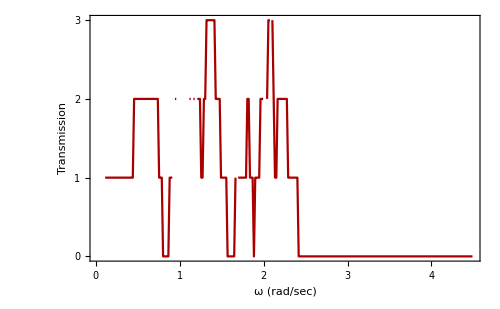

```mathematica
(****************************************** Parameters ********************************)
mChannel =1(*.12*); mSource=1(*.047*); mDrain=mSource;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;

kVerticalChannel = 1;kHorizontalChannel = 1.(*13.7*);
kVerticalSource=1;kHorizontalSource= 1.(*15.3*);
kVerticalDrain=kVerticalSource; kHorizontalDrain=kHorizontalSource;
kSC =1. (*15.3*)(*(kHorizontalChannel+kHorizontalSource)/2*); kCD = kSC (*(kHorizontalChannel+kHorizontalDrain)/2*);
η=0.000001;
surfaceElements1=Sort@Table[i,{i,1,14}];

(****************************************** dynamical Matrix ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
KChannel = Table[If[r==c,If[(MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]]) || (MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]]),kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@latticeCoordinates},{c, 1, Length@latticeCoordinates}];

(**********************************Couplings******************************************)
cSource = Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
cDrain = cSource;

(**********************************Leads******************************************)
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
αDrain= αSource;

βSource=Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}];
βDrain=βSource;

Map[MatrixForm,{KChannel,cSource,αSource,βSource}];

(************************************ Transmission Calculation ********************************************)
transmission=ParallelTable[
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSC ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mCD ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.βDrain.GS11.ConjugateTranspose[βDrain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}]];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(Length@surfaceElements1-1),cDrain.Partition[Values[sol],{Length@cDrain}].ConjugateTranspose[cDrain],0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[(mChannel IdentityMatrix[Length@KChannel] ω1^2 - KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.11,4.5,.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

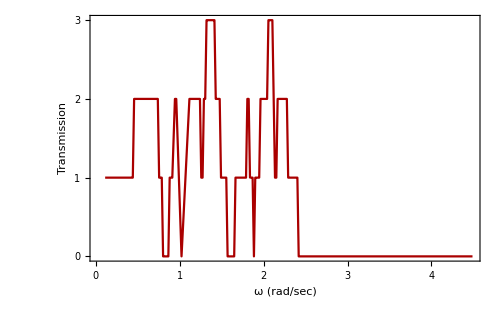

```mathematica
transmission =Select[transmission,Im[#[[2]]]==0&];
tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

## 3 D Lattice Phonon

### Model - 3D

```mathematica
(*********************************************Function to generate spring between two points*********************************************)generateSpring[p1_,p2_,turns_,springRadius_,tubeRadius_]:=Module[{vector,length,direction,helixPath,alignmentMatrix},vector=p2-p1;
length=Norm[vector];
(*Handle the degenerate case where the points coincide*)If[length==0,Return[Graphics3D[]]];
direction=vector/length;(*Normalize the direction vector*)helixPath=Table[{springRadius Cos[2 Pi turns z/length],springRadius Sin[2 Pi turns z/length],z},{z,0,length,0.01}];(*Helical path along the z-axis*)alignmentMatrix=RotationMatrix3D[VectorAngle[{0,0,1},direction],Cross[{0,0,1},direction]];
helixPath=Map[alignmentMatrix.#+p1&,helixPath];(*Apply the alignment and translate the helix to p1*)Graphics3D[{Black,Tube[helixPath,tubeRadius]}]];

(*Rotation matrix in 3D for a given axis and angle*)
RotationMatrix3D[angle_,axis_]:=Module[{c=Cos[angle],s=Sin[angle],v=1-Cos[angle],x,y,z},{x,y,z}=Normalize[axis];
{{x x v+c,x y v-z s,x z v+y s},{x y v+z s,y y v+c,y z v-x s},{x z v-y s,y z v+x s,z z v+c}}];

(*********************************************Function to generate Lattice coordinates******************************************************)

cubicLatticeCoordinates[length_,width_,height_,ax_,ay_,az_]:=Module[{coordinates},coordinates=Table[{i*ax,j*ay,k*az},{i,0,length-1},{j,0,width-1},{k,0,height-1}];
Flatten[coordinates,2]];

(*********************************************Function to generate hoppings along x,y,and z directions*********************************************)

generateHoppings[coordinates_,ax_,ay_,az_]:=Module[{hoppings,neighbors,xHop,yHop,zHop,tx=1,ty=1,tz=1},
xHop={tx,{ax,0,0}};
yHop={ty,{0,ay,0}};
zHop={tz,{0,0,az}};
hoppings=Flatten[Table[neighbors={};
If[MemberQ[coordinates,coord+xHop[[2]]],AppendTo[neighbors,{coord,coord+xHop[[2]]}]];
If[MemberQ[coordinates,coord+yHop[[2]]],AppendTo[neighbors,{coord,coord+yHop[[2]]}]];
If[MemberQ[coordinates,coord+zHop[[2]]],AppendTo[neighbors,{coord,coord+zHop[[2]]}]];
neighbors,{coord,coordinates}],1];
hoppings];

(*******************************Parameters***********************************)

length=3;width=3;height=3;
ax=1;ay=1;az=1;
latticeCoordinates=SortBy[cubicLatticeCoordinates[length,width,height,ax,ay,az],First];
hoppings=generateHoppings[latticeCoordinates,ax,ay,az];

(*******************************Final Plot***********************************)

masses=Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[latticeCoordinates[[i]],0.2]},Boxed->False],{i,1,Length@latticeCoordinates}],ViewPoint->Above,ImageSize->700];
springs=Show[Table[generateSpring[hoppings[[i,1]],hoppings[[i,2]],8,0.05,0.01],{i,1,Length@hoppings}]];
label=Show[Table[Graphics3D[Text[Style[i,20,White],latticeCoordinates[[i]]]],{i,1,Length[latticeCoordinates]}]];
Show[masses,springs,label]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= ax&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=ax&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[latticeCoordinates];
NNHI=nearestNeighborsIndex[latticeCoordinates]
```

-Graphics3D-

{{1,{2,4,10}},{2,{1,3,5,11}},{3,{2,6,12}},{4,{1,5,7,13}},{5,{2,4,6,8,14}},{6,{3,5,9,15}},{7,{4,8,16}},{8,{5,7,9,17}},{9,{6,8,18}},{10,{1,11,13,19}},{11,{2,10,12,14,20}},{12,{3,11,15,21}},{13,{4,10,14,16,22}},{14,{5,11,13,15,17,23}},{15,{6,12,14,18,24}},{16,{7,13,17,25}},{17,{8,14,16,18,26}},{18,{9,15,17,27}},{19,{10,20,22}},{20,{11,19,21,23}},{21,{12,20,24}},{22,{13,19,23,25}},{23,{14,20,22,24,26}},{24,{15,21,23,27}},{25,{16,22,26}},{26,{17,23,25,27}},{27,{18,24,26}}}

### Transmission

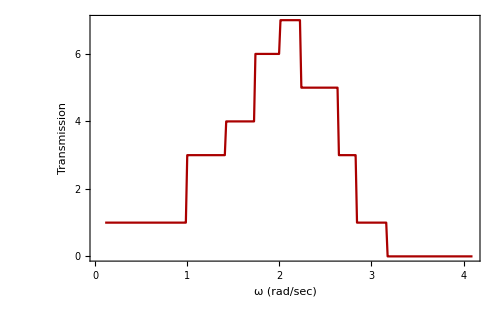

```mathematica
(****************************************** Parameters ********************************)
mChannel =1(*.12*); mSource=1(*.047*); mDrain=mSource;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;

kVerticalChannel = 1;kHorizontalChannel = 1(*13.7*);
kVerticalSource=1;kHorizontalSource= 1(*15.3*);
kVerticalDrain=kVerticalSource; kHorizontalDrain=kHorizontalSource;
kSC =1 (*15.3*)(*(kHorizontalChannel+kHorizontalSource)/2*); kCD = kSC (*(kHorizontalChannel+kHorizontalDrain)/2*);
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,9}];

(****************************************** dynamical Matrix ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
KChannel = Table[If[r==c,If[(MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]]) || (MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]]),kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@latticeCoordinates},{c, 1, Length@latticeCoordinates}];

(**********************************Couplings******************************************)
cSource = Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
cDrain = cSource;

(**********************************Leads******************************************)
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
αDrain=Table[If[r==c,If[latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]},{c, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]}];

βSource=Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}];
βDrain=βSource;

Map[MatrixForm,{KChannel,cSource,αSource,αDrain,βSource}];

(************************************ Transmission Calculation ********************************************)
transmission=ParallelTable[
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSC ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mCD ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.βDrain.GS11.ConjugateTranspose[βDrain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}]];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(Length@surfaceElements1-1),cDrain.Partition[Values[sol],{Length@cDrain}].ConjugateTranspose[cDrain],0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[(mChannel IdentityMatrix[Length@KChannel] ω1^2 - KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.11,4.1,.0151}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```

```mathematica
Map[MatrixForm,{ΓS,ΓD}];
```